This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 12 Analytic Continuation of the Beta function via the Pochhammer contour Integral for Rational Exponents ch12RationalBeta.nb

## Other info

```mathematica
newP=Numerator@Simplify[3/6]
newQ=Denominator@Simplify[3/6]
```

1

2

```mathematica
theP=1;
theQ=4;
theR=7;
theS=3
If[GCD[theR,theS]!=1,
Print["not in lowest terms"];
cd=GCD[theR,theS];
theR=theR/cd;
theS=theS/cd;
];

If[GCD[theP,theQ]!=1,
Print["not in lowest terms"];
cd=GCD[theP,theQ];
theP=theP/cd;
theQ=theQ/cd;
];
theM=LCM[theQ,theS];
Print["theM: ",theM];
aTable=Table[{j,k,Exp[2 Pi I(theP/theQ j+theR/theS k)]},
{j,0,theQ-1},
{k,0,theS-1}]
```

3

theM: 12

{{{0,0,1},{0,1,ⅇ^((2 ⅈ π)/3)},{0,2,ⅇ^(-(2 ⅈ π)/3)}},{{1,0,ⅈ},{1,1,ⅇ^(-(5 ⅈ π)/6)},{1,2,ⅇ^(-(ⅈ π)/6)}},{{2,0,-1},{2,1,ⅇ^(-(ⅈ π)/3)},{2,2,ⅇ^((ⅈ π)/3)}},{{3,0,-ⅈ},{3,1,ⅇ^((ⅈ π)/6)},{3,2,ⅇ^((5 ⅈ π)/6)}}}

```mathematica
G[z_]:=z^(theP/theQ)(1-z)^(theR/theS);
G[z]
H[z_,j_,k_]:=Abs[z]^(theP/theQ) Exp[theP I/theQ(Arg[z]+2 j Pi)] Abs[1-z]^(theR/theS) Exp[theR I/theS(Arg[1-z]+2k Pi)];

Flatten[aTable,1]
bTable=Table[Exp[2 n Pi I/theM],{n,0,theM-1}]
onePos=Position[Flatten[aTable,1],{a_,b_,c_}/;c==#]&/@ bTable
```

(1-z)^(7/3) z^(1/4)

{{0,0,1},{0,1,ⅇ^((2 ⅈ π)/3)},{0,2,ⅇ^(-(2 ⅈ π)/3)},{1,0,ⅈ},{1,1,ⅇ^(-(5 ⅈ π)/6)},{1,2,ⅇ^(-(ⅈ π)/6)},{2,0,-1},{2,1,ⅇ^(-(ⅈ π)/3)},{2,2,ⅇ^((ⅈ π)/3)},{3,0,-ⅈ},{3,1,ⅇ^((ⅈ π)/6)},{3,2,ⅇ^((5 ⅈ π)/6)}}

{1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1,ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6)}

{{{1}},{{11}},{{9}},{{4}},{{2}},{{12}},{{7}},{{5}},{{3}},{{10}},{{8}},{{6}}}

```mathematica
rootTable=Table[
links=(aTable[[Sequence@@#]]&/@ onePos[[k]])[[All,1;;2]];
{k-1,links},
{k,1,Length@bTable}
];
Grid[Prepend[rootTable,{"Root index","(j,k)"}],Dividers->{{{True}},{True,True,{False},True}}]
```

Part::take: Cannot take positions 1 through 2 in {{0,0,1}}.

Part::take: Cannot take positions 1 through 2 in {{1,0,-1}}.

Root index | (j,k)
0 | {{{0,0,1}}}⟦All,1;;2⟧
1 | {{{1,0,-1}}}⟦All,1;;2⟧

```mathematica
tableIndex=6;
rootIndex=rootTable[[tableIndex,1]];
jkIndex=3;
baseF[z_]:= Exp[2 Pi I rootIndex/theM] G[z];
p1=ParametricPlot3D[{Re@z,Im@z,Re@H[z,Sequence@@rootTable[[tableIndex,2,3]]]}/.z->r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1}];
p2=ParametricPlot3D[{Re@z,Im@z,Re@H[z,Sequence@@rootTable[[tableIndex,2,3]]]}/.z->r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1}];
Show[{p1,p2},PlotRange->All,BoxRatios->{1, 1, 1}]

p1=ParametricPlot3D[{Re@z,Im@z,Re@baseF[z]}/.z->r Exp[I t],{r,0,2},{t,-Pi,0},BoxRatios->{1, 1, 1}];
p2=ParametricPlot3D[{Re@z,Im@z,Re@baseF[z]}/.z->r Exp[I t],{r,0,2},{t,0,Pi},BoxRatios->{1, 1, 1}];
Show[{p1,p2},PlotRange->All,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

-Graphics3D-

## Study of Beta Residue Theorem:

```mathematica
subDirectory="betaResidueCase";
$theTestCase=subDirectory;

 theP=1;
theQ=3;
theR=7;
theS=4;
G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)
H[z_,j_,k_]:=Abs[z]^(theP/theQ) Exp[theP I/theQ(Arg[z]+2 j Pi)] Abs[1-z]^(theR/theS) Exp[theR I/theS(Arg[1-z]+2k Pi)];

theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
theFunction=theG fact1 fact2-theW;
Print["theFunction: ",aForm[theFunction]]


radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];

aForm[theFunction]




wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 12

(1-z)^21 z^4

theW: w^12

theFunction: (z^4-21 z^5+210 z^6-1330 z^7+5985 z^8-20349 z^9+54264 z^10-116280 z^11+203490 z^12-293930 z^13+352716 z^14-352716 z^15+293930 z^16-203490 z^17+116280 z^18-54264 z^19+20349 z^20-5985 z^21+1330 z^22-210 z^23+21 z^24-1 z^25)+(-1) w^12

theAlpha: 4/3

theBeta: 11/4

(z^4-21 z^5+210 z^6-1330 z^7+5985 z^8-20349 z^9+54264 z^10-116280 z^11+203490 z^12-293930 z^13+352716 z^14-352716 z^15+293930 z^16-203490 z^17+116280 z^18-54264 z^19+20349 z^20-5985 z^21+1330 z^22-210 z^23+21 z^24-1 z^25)+(-1) w^12

12

0

0

```mathematica
(* plot homocyclic principal branch in upper half-plane*)
p1=ParametricPlot3D[{Re@z,Im@z,Re@ H[z,0,0]}/.z->r Exp[I t],{r,0,1},{t,0,Pi},PlotStyle->{Opacity[0.5],Red}];
p2=ParametricPlot3D[{Re@z,Im@z,Re@ H[z,0,0]}/.z->r Exp[I t],{r,1,2},{t,0,Pi},PlotStyle->{Opacity[0.5],Green}];
(* plot branches in lower half-plane *)
p1b=ParametricPlot3D[{Re@z,Im@z,Re@(Exp[2 Pi I theP/theQ] H[z,0,0])}/.z->r Exp[I t],{r,0,1},{t,-Pi,0},PlotStyle->{Opacity[0.5],Red}];
p2b=ParametricPlot3D[{Re@z,Im@z,Re@(Exp[2 Pi I theP/theQ] H[z,0,0])}/.z->r Exp[I t],{r,1,2},{t,-Pi,0},PlotStyle->{Opacity[0.5],Green}];
Show[{p1,p1b,p2,p2b},PlotRange->2,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
(*
 first IVP from G(1/4) to z=1/4+3/2/i
*)
yStart=0;
yEnd=3/2;
 
theZ[y_]:=1/4+y I;

wStart=G[theZ[yStart]];
Print["wStart: ",wStart//N];

wDeriv=w'[y]==((-(D[theFunction,z]/D[theFunction,w]) (D[theZ[y],y]))/.{w->w[y],z->theZ[y]});


solY=NDSolveValue[{wDeriv,w[yStart]==wStart},w,{y,yStart,yEnd},MaxStepSize->500];
solYPlot=ParametricPlot3D[{Re@z,Im@z,Re@solY[t]}/.z->theZ[t],{t,yStart,yEnd},PlotStyle->Black];
branchW0=solY[yEnd]

branchW0
branchVals=Table[{n,Exp[2 n Pi I/theQ]H[theZ[yEnd],0,0]//N},
{n,0,theQ-1}
]

Show[{solYPlot,p1,p1b,p2,p2b},PlotRange->2,BoxRatios->{1, 1, 1}]
```

wStart: 0.343682

1.5881+0.640806 ⅈ

1.5881+0.640806 ⅈ

{{0,1.5881+0.640806 ⅈ},{1,-1.34901+1.05493 ⅈ},{2,-0.239096-1.69574 ⅈ}}

-Graphics3D-

```mathematica
(*
 next, generate medial contour for branch expansions
*)

 tStart=Pi/2;
tEnd=5 Pi/2;
rVal=3/2;
zStart=rVal Exp[ⅈ tStart];

theZ[t_]:=1/4+rVal Exp[I t];

branchW0=H[theZ[tStart],0,0];

wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});


solF=NDSolveValue[{wDeriv,w[tStart]==branchW0},w,{t,tStart,tEnd},MaxStepSize->500];
solPlot=ParametricPlot3D[{Re@z,Im@z,Re@solF[t]}/.z->theZ[t],{t,tStart+0.05,tEnd-0.05},PlotStyle->Black];

arrowPoints=Table[{Re@z,Im@z,Re@solF[t]}/.z->theZ[t],{t,tStart,tStart+3/4,0.01}];
arrowG=Graphics3D@{Arrow[BSplineCurve[arrowPoints]]};
startPtG=Graphics3D@{PointSize[0.025],Yellow,Point@{Re@theZ[tStart],Im@theZ[tStart],Re@solF[tStart]}};
s1G=Graphics3D@{PointSize[0.025],Red,Point[{0,0,0}]};
s2G=Graphics3D@{PointSize[0.025],Cyan,Point[{1,0,0}]};
Show[{p1,p1b,p2,p2b,solPlot,arrowG,startPtG,s1G,s2G},PlotRange->2,BoxRatios->{1, 1, 1}]
 (*
 now define a_{-1} 1/(2 Pi i) Integral of solF[t]d/dt C(t)dt
*)
intVal=NIntegrate[solF[t] D[theZ[t],t],{t,tStart,tEnd}]


intVal/(Exp[2 Pi I(theP/theQ)]-1)
Beta[1+theP/theQ,1+theR/theS]//N
```

-Graphics3D-

-1.19988-1.64597 ⅈ

1.07509+0.476607 ⅈ

0.341157

```mathematica
p1=ParametricPlot3D[{Re@z,Im@z,Re@H[z,0,0]}/.z->r Exp[I t],{r,0,1},{t,0,Pi},PlotStyle->{Opacity[0.5],Red}];
p1b=ParametricPlot3D[{Re@z,Im@z,Re@H[z,1,0]}/.z->r Exp[I t],{r,0,1},{t,-Pi,0},PlotStyle->{Opacity[0.5],Red}];
p2=ParametricPlot3D[{Re@z,Im@z,Re@H[z,1,0]}/.z->r Exp[I t],{r,1,2},{t,-Pi,0},PlotStyle->{Opacity[0.5],Green}];
p2b=ParametricPlot3D[{Re@z,Im@z,Re@H[z,0,0]}/.z->r Exp[I t],{r,1,2},{t,0,Pi},PlotStyle->{Opacity[0.5],Green}];
Show[{p1,p1b,p2,p2b,solYPlot},PlotRange->All,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
(*
 next, generate medial contour for branch expansions
*)

 tStart=Pi/2;
tEnd=5 Pi/2;
rVal=3/2;
zStart=rVal Exp[ⅈ tStart];

theZ[t_]:=1/4+rVal Exp[I t];



wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});


solF=NDSolveValue[{wDeriv,w[tStart]==branchW0},w,{t,tStart,tEnd},MaxStepSize->500];
solPlot=ParametricPlot3D[{Re@z,Im@z,Re@solF[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->Yellow];
 (*
 now define a_{-1} 1/(2 Pi i) Integral of solF[t]d/dt C(t)dt
*)
intVal=NIntegrate[solF[t] D[theZ[t],t],{t,tStart,tEnd}]


intVal/(Exp[2 Pi I(theP/theQ)]-1)
Beta[1+theP/theQ,1+theR/theS]//N
```

-0.785397-2.36995×10^-7 ⅈ

0.392699+1.18497×10^-7 ⅈ

0.392699

```mathematica
FullSimplify@branchW0
asmVals=FullSimplify[asmSeries/.z->(1/4+3/2 Exp[Pi I/2])];
branchW0//N
asmVals//N
branchW0===asmVals[[3]]
```

1/4 (-471+1022 ⅈ)^(1/5) 3^(2/5)

1.45624+0.616599 ⅈ

{-0.136416+1.57551 ⅈ,-0.815699-1.3548 ⅈ,1.45624+0.616599 ⅈ,-1.54055+0.35712 ⅈ,1.03642-1.19443 ⅈ}

False

-\frac{3}{25}, -\frac{3}{25}(-1)^{4/5}, \frac{3}{25}(-1)^{3/5},-\frac{3}{25}(-1)^{2/5}, \frac{3}{25}(-1)^{1/5}

```mathematica
asmSeries=w/. AsymptoticSolve[theFunction==0,w,{z,∞,50}];
cList=Coefficient[asmSeries,z,-1]
TrigExpand@cList
asmValues=asmSeries/.z->1/4+3/2 Exp[Pi I/2];
asmValues//N
branchW0//N
```

{-ⅈ/8,ⅈ/8}

{-ⅈ/8,ⅈ/8}

{-1.5792-0.237461 ⅈ,1.5792+0.237461 ⅈ}

1.5792+0.237461 ⅈ

```mathematica
cList[[3]]
cList[[3]]//N
3/25 Exp[theP I/theQ(Pi+2 # Pi)]&/@{0,1,2,3,4}//N
```

3/25 (-1)^(3/5)

-0.037082+0.114127 ⅈ

{-0.037082+0.114127 ⅈ,0.097082-0.0705342 ⅈ,-0.12,0.097082+0.0705342 ⅈ,-0.037082-0.114127 ⅈ}

```mathematica
(2 Pi I cList[[2]])/(Exp[2 Pi I(theP/theQ)]-1)//FullSimplify
Beta[3/2,3/2]
```

π/8

π/8

```mathematica
(2 Pi I cList[[2]])/(Exp[2 Pi I(theP/theQ)]-1)//N
Beta[theAlpha,theBeta]//N
N[(2 Pi I 3/25 Exp[3/5 Pi I])/(Exp[2 Pi I(3/5)]-1),35]
N[Beta[theAlpha,theBeta],35]
sVal=(2 Pi I 3/25 Exp[3/5 Pi I])/(Exp[2 Pi I(3/5)]-1)//FullSimplify
Beta[8/5,7/5]===sVal
gVal=(Gamma[theAlpha] Gamma[theBeta])/Gamma[theAlpha+theBeta]//FullSimplify
N[sVal,50]
N[gVal,50]
```

0.396392-2.77556×10^-17 ⅈ

0.396392

0.39639191990329489262230785552621842+0. ⅈ

0.39639191990329489262230785552621842

3/25 √(2-2/(√5)) π

False

1/2 Gamma[7/5] Gamma[8/5]

0.39639191990329489262230785552621842050507211312283

0.39639191990329489262230785552621842050507211312283

```mathematica
sVal=(2 Pi I 3/25 Exp[3/5 Pi I])/(Exp[2 Pi I(3/5)]-1)//FullSimplify
Beta[8/5,7/5]===sVal
```

```mathematica
3/5.
Beta[8/5,7/5]//N
(6/25 Pi I Exp[Pi I theP/theQ])/(Exp[2 Pi I theAlpha]-1)//N
```

0.6

0.396392

0.396392-6.93889×10^-17 ⅈ

```mathematica
FindRoot[Beta[1+z,7/5]==(6/25 Pi I Exp[Pi I z])/(Exp[2 Pi I z]-1),{z,0.6}]
```

{z→0.6}

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Beta[1+z,7/5]==(6 ⅈ ⅇ^(ⅈ π z) π)/(25 (-1+ⅇ^(2 ⅈ π z))),z]

```mathematica
precisionVal=20
theK=-1;
rNorm=3/2
 theInt=Plus@@Table[
NIntegrate[solF[t](Cos[t theK]-I Sin[t theK]),{t,tStart,tEnd},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,1}
];
rNorm/(2 Pi) theInt
```

20

3/2

-0.037082052501548855734+0.11412679897760672042 ⅈ

```mathematica
(*
 now generate branch expansions
*)
termRange=Range[-5,5];
precisionVal=20;
$selectedBranchSize=1;
rNorm=3/2;
seriesTable=Table[
If[Mod[k,5]==0,
Print[k];
];
If[k==0,
finalIntVal=Plus@@Table[
NIntegrate[solF[t](Cos[t k]-I Sin[t k]),{t,tStart,tEnd},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"GaussKronrodRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,1}
];
,
finalIntVal=Plus@@Table[
NIntegrate[solF[t](Cos[t k]-I Sin[t k]),{t,tStart,tEnd},Method->{"GlobalAdaptive","MaxErrorIncreases"->600,Method->"LevinRule"},WorkingPrecision->precisionVal,AccuracyGoal->precisionVal/2,MaxRecursion->Infinity],
{index,1,1}
];
];
coef=1/(2 Pi $selectedBranchSize rNorm^(k/$selectedBranchSize))finalIntVal;
{k/$selectedBranchSize,coef,N[coef,10],coef (z^(1/$selectedBranchSize))^k},
{k,termRange}
];
```

-5

0

5

### Study of Theorem 2 with circular contour:

```mathematica
subDirectory="tempBetaCase";
$theTestCase=subDirectory;

 theP=-5;
theQ=3;
theR=8;
theS=3;
G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
theFunction=theG fact1 fact2-theW;
Print["theFunction: ",aForm[theFunction]]


radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];

aForm[theFunction]




wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

fact1: z^5

fact2: 1

theM: 3

(1-z)^8/z^5

theW: w^3 z^5

theFunction: (1-8 z+28 z^2-56 z^3+70 z^4-56 z^5+28 z^6-8 z^7+1 z^8)+(-z^5) w^3

theAlpha: -2/3

theBeta: 11/3

(1-8 z+28 z^2-56 z^3+70 z^4-56 z^5+28 z^6-8 z^7+1 z^8)+(-z^5) w^3

3

-8

0

```mathematica
yStart=0;
yEnd=3/2;
 
theZ[y_]:=1/4+y I;

wStart=G[theZ[yStart]];
Print["wStart: ",wStart//N];

wDeriv=w'[y]==((-(D[theFunction,z]/D[theFunction,w]) (D[theZ[y],y]))/.{w->w[y],z->theZ[y]});


solY=NDSolveValue[{wDeriv,w[yStart]==wStart},w,{y,yStart,yEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
solYPlot=ParametricPlot3D[{Re@z,Im@z,Re@solY[t]}/.z->theZ[t],{t,yStart,yEnd},PlotStyle->Yellow];
newWStart=solY[yEnd];
```

wStart: 4.68019

```mathematica
tStart=Pi/2;
tEnd=5 Pi/2;
rVal=3/2;
zStart=rVal Exp[ⅈ tStart];

theZ[t_]:=1/4+rVal Exp[I t];



wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});


solF=NDSolveValue[{wDeriv,w[tStart]==newWStart},w,{t,tStart,tEnd},MaxSteps->totalIntegrationSteps,MaxStepSize->maxStepSize];
solPlot=ParametricPlot3D[{Re@z,Im@z,Re@solF[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->Yellow];
intVal=NIntegrate[solF[t] D[theZ[t],t],{t,tStart,tEnd}]
Beta[theAlpha,theBeta]//N
1/(Exp[2 Pi I(theP/theQ)]-1) intVal//N
```

12.092-6.98132 ⅈ

-8.06133

-8.06133-7.26658×10^-8 ⅈ

```mathematica
p1=ParametricPlot3D[{Re@z,Im@z,Re@H[z,1,0]}/.z->r Exp[I t],{r,1,2},{t,-Pi,0}];
p2=ParametricPlot3D[{Re@z,Im@z,Re@H[z,0,0]}/.z->r Exp[I t],{r,1,2},{t,0,Pi}];
p3=ParametricPlot3D[{Re@z,Im@z,Re@H[z,1,1]}/.z->r Exp[I t],{r,0.2,1},{t,0,Pi},PlotStyle->Blue];
p4=ParametricPlot3D[{Re@z,Im@z,Re@H[z,0,0]}/.z->r Exp[I t],{r,0.2,1},{t,-Pi,0},PlotStyle->Green];
Show[{p2,p3,solPlot,solYPlot},PlotRange->3,AxesLabel->{"x","y","z"},BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### Study of figure-8 contour

```mathematica
subDirectory="tempBetaCase";
$theTestCase=subDirectory;

 theP=3;
theQ=1;
theR=2;
theS=1;
Print["(p/q-r/w): ",theP/theQ-theR/theS];

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS);

theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
(*Print["fact1: ",fact1];
Print["fact2: ",fact2];
*)
theM=LCM[theQ,theS];
(*Print["theM: ",theM];*)
theG=G[z]^theM;
theW=fact1 fact2 w^theM;
(*Print["theW: ",theW];*)
theFunction=theG fact1 fact2-theW;
(*Print["theFunction: ",aForm[theFunction]];*)


radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction;
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

(*Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];

aForm[theFunction];
*)



wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp;

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}

 tStart=-Pi;
tEnd=Pi;

theZ[t_]:=(Sin[t]+1/2)+I(Sin[t] Cos[t]);

wStart=G[theZ[tStart]];


wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) (D[theZ[t],t]))/.{w->w[t],z->theZ[t]});


solF=NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxStepSize->1/5500];
solPlot=ParametricPlot3D[{Re@z,Im@z,Re@solF[t]}/.z->theZ[t],{t,tStart,tEnd},PlotStyle->Yellow,PlotRange->All,BoxRatios->{1, 1, 1}]
intVal=NIntegrate[solF[t] D[theZ[t],t],{t,tStart,tEnd}];
Print["intVal: ",intVal];
Print["Beta: ",Beta[theAlpha,theBeta]//N]
Print["beta at integer: ",Beta[1+theP/theQ,1+theR/theS]//N];
Print["beta integral expression: ",1/(Exp[2 Pi I(theP/theQ)]-1) intVal//N]
```

(p/q-r/w): 1

0

-1

-Graphics3D-

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-3.1412402234069948584707816785499545630955253727734088897705078125}. NIntegrate obtained 1.83957×10^-12+1.84789×10^-12 ⅈ and 2.87429×10^-13 for the integral and error estimates.

intVal: 1.83957×10^-12+1.84789×10^-12 ⅈ

Beta: 0.0166667

beta at integer: 0.0166667

Power::infy: Infinite expression 1/0 encountered.

beta integral expression: ComplexInfinity

wStart: 4.68019

-Graphics3D-

intVal: -0.0443239+0.27985 ⅈ

Beta: 0.905612

beta integral expression: 0.905612+2.63441×10^-7 ⅈ

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
p1=ParametricPlot3D[{Re@z,Im@z,Re@H[z,1,0]}/.z->r Exp[I t],{r,1,2},{t,-Pi,0}];
p2=ParametricPlot3D[{Re@z,Im@z,Re@H[z,0,0]}/.z->r Exp[I t],{r,1,2},{t,0,Pi}];
p3=ParametricPlot3D[{Re@z,Im@z,Re@H[z,1,1]}/.z->r Exp[I t],{r,0.2,1},{t,0,Pi},PlotStyle->Blue];
p4=ParametricPlot3D[{Re@z,Im@z,Re@H[z,0,0]}/.z->r Exp[I t],{r,0.2,1},{t,-Pi,0},PlotStyle->Green];
Show[{p2,p3,solPlot,solYPlot},PlotRange->3,AxesLabel->{"x","y","z"},BoxRatios->{1, 1, 1}]
```

-Graphics3D-

## Section 1: Beta test cases

### testCase0039: z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)
H[z_,j_,k_]:=Abs[z]^(theP/theQ) Exp[theP I/theQ(Arg[z]+2 j Pi)] Abs[1-z]^(theR/theS) Exp[theR I/theS(Arg[1-z]+2 k Pi)];

radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
saveFunction=theFunction;

aForm[theFunction]

wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

2

### testCase0040: z^(1/3)(1-z)^(1/2)

```mathematica
subDirectory="testCase0040";
$theTestCase=subDirectory;


 theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)
H[z_,j_,k_]:=Abs[z]^(theP/theQ) Exp[theP I/theQ(Arg[z]+2 j Pi)] Abs[1-z]^(theR/theS) Exp[theR I/theS(Arg[1-z]+2 k Pi)];

radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;
alphaCycleSize=3;
betaCycleSize=2;



Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
saveFunction=theFunction;

aForm[theFunction]

wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp


reim=Im;
```

fact1: 1

fact2: 1

theM: 6

G[z]^6

theW: w^6

-w^6+G[z]^6

theAlpha: 4/3

theBeta: 3/2

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

### testCase0041: z^(1/3)(1-z)^(1/4)

```mathematica
G[z_]:=z^(1/3)(1-z)^(1/4)
H[z_,k_,j_]:=Abs[z]^(1/3) Exp[I/3(Arg[z]+2 k Pi)] Abs[1-z]^(1/4) Exp[I/4(Arg[1-z]+2j Pi)];

gb= GroebnerBasis[z^(1/3)(1-z)^(1/4)==w,z]

radicalF[z_]:=z^(1/3)(1-z)^(1/4);
theAlpha=4/3;
theBeta=5/4;
alphaCycleSize=3;
betaCycleSize=4;
theFunction=gb[[1]]
implicitF[z_,w_]:=theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;

aForm[z^4(1-z)^3-w^12]
aForm[theFunction]

wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
aForm[theFunction]//TeXForm
```

{w^12-z^4+3 z^5-3 z^6+z^7,w^8 z^(1/3)-z^3+2 z^4-z^5,w^4-z^(4/3)+z^(7/3),w^4 z^(2/3)-z^2+z^3,w^3 (1-z)^(1/4)-z+z^2,-w z^(2/3)+(1-z)^(1/4) z,-w+(1-z)^(1/4) z^(1/3),w^2 √(1-z)-z^(2/3)+z^(5/3),w (1-z)^(3/4)-z^(1/3)+z^(4/3)}

w^12-z^4+3 z^5-3 z^6+z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

(-z^4+3 z^5-3 z^6+1 z^7)+(1) w^12

12

0

0

\left(-z^4+3 z^5-3 z^6+1 z^7\right)+(1) w^{12}

```mathematica
p1=ParametricPlot3D[{Re@z,Im@z,Im@H[z,0,0]}/.z->r Exp[I t],{r,0,2},{t,-Pi,0},PlotStyle->{Opacity[0.5],Yellow}];
p1b=ParametricPlot3D[{Re@z,Im@z,Im@H[z,0,0]}/.z->r Exp[I t],{r,0,2},{t,0,Pi},PlotStyle->{Opacity[0.5],Green}];
p2=ParametricPlot3D[{Re@z,Im@z,Im@H[z,0,1]}/.z->r Exp[I t],{r,0,2},{t,-Pi,0},PlotStyle->{Opacity[0.5],Blue}];
p2b=ParametricPlot3D[{Re@z,Im@z,Im@H[z,0,1]}/.z->r Exp[I t],{r,0,2},{t,0,Pi},PlotStyle->{Opacity[0.5],Orange}];
Show[{p2,p2b},PlotRange->All,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

### testCase0043: z^(5/3)(1-z)^(5/7)

```mathematica
subDirectory="testCase0043";
$theTestCase=subDirectory;



 theP=5;
theQ=3;
theR=5;
theS=7;
G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

H[z_,k_,j_]:=Abs[z]^(theP/theQ) Exp[theP I/theQ(Arg[z]+2 k Pi)] Abs[1-z]^(theR/theS) Exp[theR I/theS(Arg[1-z]+2j Pi)];

theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
theFunction=theG fact1 fact2-theW;
Print["theFunction: ",aForm[theFunction]]
alphaCycleSize=7;
betaCycleSize=3;


implicitF[z_,w_]:=theFunction



radicalF[z_]:=G[z];
implicitF[z_,w_]:=theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];

aForm[theFunction]




wExp=Exponent[theFunction,w,List];
functionDegree=Last@wExp
```

fact1: 1

fact2: 1

theM: 21

(1-z)^15 z^35

theW: w^21

theFunction: (z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

theAlpha: 8/3

theBeta: 12/7

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

## Section 2: Import power expansions at both singular points

```mathematica
(*
 retrieve singular points from file
*)
If[FileExistsQ[singularDataFileName[$theTestCase]],
theData=Import[singularDataFileName[$theTestCase]];
{theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes,nearestDistanceArray,rNormArray}=theData;

Print["Total singular points: ",Length@theSingularList];

Print["Precision of singular points: ",Precision@theSingularList];Print["Total poles: ",Length@poleIndexes];
Print[Style["s_p indexes: ",Red],Style[poleIndexes,Red]];
Print[Style["s_q indexes: ",Red],Style[zeroIndexes,Blue]];
Print["theSingularList: ",theSingularList//N];
(*
 import series data
*)
baseSingularIndex=1;
 If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],

baseSingularPoint=theSingularList[[baseSingularIndex]]; 
baseRadius=minRadiusArray[[baseSingularIndex]];
Print["baseSingularPoint: ",theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[$theTestCase,baseSingularIndex]];
dataList=Import[seriesFileName[$theTestCase,baseSingularIndex]];
Print["Len dataList: ",Length@dataList];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
,
Print[Style[seriesFileName[$theTestCase,baseSingularIndex]<>" not found during import.",Red]];
];
Print["baseBranchTypeArray: ",baseBranchTypeArray];
Print["baseSeriesMIVPTable: ",baseSeriesMIVPTable];

zeroBaseSeries=baseSeries;
Print["Size of series at s_1: ",Length@zeroBaseSeries[[1]]];
Print[zeroBaseSeries[[All,1;;6]]//N//MatrixForm];
zeroBranchTypeArray=baseBranchTypeArray;
zeroMIVTable=baseSeriesMIVPTable;
zeroMinRadiusArray=minRadiusArray;
Print["zeroMIVTable: ",zeroMIVTable];
(*
 s_2=1
*)
 
baseSingularIndex=2;
 If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],

baseSingularPoint=theSingularList[[baseSingularIndex]]; 
baseRadius=minRadiusArray[[baseSingularIndex]];
Print["baseSingularPoint: ",theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[$theTestCase,baseSingularIndex]];
dataList=Import[seriesFileName[$theTestCase,baseSingularIndex]];
(*Print["Len dataList: ",Length@dataList];*)
baseBranchTypeArray={};
baseSeriesMIVPTable={};
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
,
Print[Style[seriesFileName[$theTestCase,baseSingularIndex]<>" not found during import.",Red]];
];
Print["baseBranchTypeArray: ",baseBranchTypeArray];
Print["baseSeriesMIVPTable: ",baseSeriesMIVPTable];

oneBaseSeries=baseSeries;
Print["Size of series at s_2: ",Length@oneBaseSeries[[1]]];
Print[baseSeries[[All,1;;6]]//N//MatrixForm];
oneBranchTypeArray=baseBranchTypeArray;
oneMIVTable=baseSeriesMIVPTable;
oneMinRadiusArray=minRadiusArray;
,
Print[Style[singularDataFileName[$theTestCase]<>" not found during import.",Red]];
];
```

Total singular points: 2

Precision of singular points: 1000.

Total poles: 0

s_p indexes: {}

s_q indexes: {1,2}

theSingularList: {0.,1.}

baseSingularPoint: 0.

Importing file: D:\algFunctionBook\data\testCase0043\1series.m

Len dataList: 11

baseBranchTypeArray: {{1F_3^5,{1,2,3}},{2F_3^5,{4,5,6}},{3F_3^5,{7,8,9}},{4F_3^5,{10,11,12}},{5F_3^5,{13,14,15}},{6F_3^5,{16,17,18}},{7F_3^5,{19,20,21}}}

baseSeriesMIVPTable: {{3,{{1,6},{2,9},{3,20}}},{3,{{4,4},{5,11},{6,18}}},{3,{{7,8},{8,7},{9,21}}},{3,{{10,2},{11,13},{12,16}}},{3,{{13,10},{14,5},{15,19}}},{3,{{16,1},{17,15},{18,14}}},{3,{{19,12},{20,3},{21,17}}}}

Size of series at s_1: 342

((-0.988831-0.149042 ⅈ) z^(5/3)+(0.706308+0.106459 ⅈ) z^(8/3)+(0.100901+0.0152084 ⅈ) z^(11/3)+(0.0432433+0.00651788 ⅈ) z^(14/3)+(0.0247105+0.0037245 ⅈ) z^(17/3)+(0.0162383+0.00244753 ⅈ) z^(20/3)
(0.365341+0.930874 ⅈ) z^(5/3)-(0.260958+0.66491 ⅈ) z^(8/3)-(0.0372797+0.0949871 ⅈ) z^(11/3)-(0.015977+0.0407088 ⅈ) z^(14/3)-(0.00912972+0.0232622 ⅈ) z^(17/3)-(0.00599953+0.0152866 ⅈ) z^(20/3)
(0.62349-0.781831 ⅈ) z^(5/3)-(0.44535-0.558451 ⅈ) z^(8/3)-(0.0636214-0.0797787 ⅈ) z^(11/3)-(0.0272663-0.0341909 ⅈ) z^(14/3)-(0.0155808-0.0195376 ⅈ) z^(17/3)-(0.0102388-0.012839 ⅈ) z^(20/3)
(-0.988831+0.149042 ⅈ) z^(5/3)+(0.706308-0.106459 ⅈ) z^(8/3)+(0.100901-0.0152084 ⅈ) z^(11/3)+(0.0432433-0.00651788 ⅈ) z^(14/3)+(0.0247105-0.0037245 ⅈ) z^(17/3)+(0.0162383-0.00244753 ⅈ) z^(20/3)
(0.62349+0.781831 ⅈ) z^(5/3)-(0.44535+0.558451 ⅈ) z^(8/3)-(0.0636214+0.0797787 ⅈ) z^(11/3)-(0.0272663+0.0341909 ⅈ) z^(14/3)-(0.0155808+0.0195376 ⅈ) z^(17/3)-(0.0102388+0.012839 ⅈ) z^(20/3)
(0.365341-0.930874 ⅈ) z^(5/3)-(0.260958-0.66491 ⅈ) z^(8/3)-(0.0372797-0.0949871 ⅈ) z^(11/3)-(0.015977-0.0407088 ⅈ) z^(14/3)-(0.00912972-0.0232622 ⅈ) z^(17/3)-(0.00599953-0.0152866 ⅈ) z^(20/3)
(-0.900969-0.433884 ⅈ) z^(5/3)+(0.643549+0.309917 ⅈ) z^(8/3)+(0.0919356+0.0442739 ⅈ) z^(11/3)+(0.039401+0.0189745 ⅈ) z^(14/3)+(0.0225148+0.0108426 ⅈ) z^(17/3)+(0.0147955+0.00712512 ⅈ) z^(20/3)
(0.0747301+0.997204 ⅈ) z^(5/3)-(0.0533786+0.712288 ⅈ) z^(8/3)-(0.00762552+0.101755 ⅈ) z^(11/3)-(0.00326808+0.0436095 ⅈ) z^(14/3)-(0.00186747+0.0249197 ⅈ) z^(17/3)-(0.0012272+0.0163758 ⅈ) z^(20/3)
(0.826239-0.56332 ⅈ) z^(5/3)-(0.590171-0.402371 ⅈ) z^(8/3)-(0.0843101-0.0574816 ⅈ) z^(11/3)-(0.0361329-0.024635 ⅈ) z^(14/3)-(0.0206474-0.0140771 ⅈ) z^(17/3)-(0.0135683-0.00925069 ⅈ) z^(20/3)
(-0.900969+0.433884 ⅈ) z^(5/3)+(0.643549-0.309917 ⅈ) z^(8/3)+(0.0919356-0.0442739 ⅈ) z^(11/3)+(0.039401-0.0189745 ⅈ) z^(14/3)+(0.0225148-0.0108426 ⅈ) z^(17/3)+(0.0147955-0.00712512 ⅈ) z^(20/3)
(0.826239+0.56332 ⅈ) z^(5/3)-(0.590171+0.402371 ⅈ) z^(8/3)-(0.0843101+0.0574816 ⅈ) z^(11/3)-(0.0361329+0.024635 ⅈ) z^(14/3)-(0.0206474+0.0140771 ⅈ) z^(17/3)-(0.0135683+0.00925069 ⅈ) z^(20/3)
(0.0747301-0.997204 ⅈ) z^(5/3)-(0.0533786-0.712288 ⅈ) z^(8/3)-(0.00762552-0.101755 ⅈ) z^(11/3)-(0.00326808-0.0436095 ⅈ) z^(14/3)-(0.00186747-0.0249197 ⅈ) z^(17/3)-(0.0012272-0.0163758 ⅈ) z^(20/3)
(-0.733052-0.680173 ⅈ) z^(5/3)+(0.523608+0.485838 ⅈ) z^(8/3)+(0.0748012+0.0694054 ⅈ) z^(11/3)+(0.0320577+0.0297452 ⅈ) z^(14/3)+(0.0183187+0.0169972 ⅈ) z^(17/3)+(0.012038+0.0111696 ⅈ) z^(20/3)
(-0.222521+0.974928 ⅈ) z^(5/3)+(0.158944-0.696377 ⅈ) z^(8/3)+(0.0227062-0.0994824 ⅈ) z^(11/3)+(0.00973124-0.0426353 ⅈ) z^(14/3)+(0.00556071-0.024363 ⅈ) z^(17/3)+(0.00365418-0.01601 ⅈ) z^(20/3)
(0.955573-0.294755 ⅈ) z^(5/3)-(0.682552-0.210539 ⅈ) z^(8/3)-(0.0975074-0.0300771 ⅈ) z^(11/3)-(0.0417889-0.0128902 ⅈ) z^(14/3)-(0.0238794-0.00736581 ⅈ) z^(17/3)-(0.0156922-0.00484039 ⅈ) z^(20/3)
(-0.733052+0.680173 ⅈ) z^(5/3)+(0.523608-0.485838 ⅈ) z^(8/3)+(0.0748012-0.0694054 ⅈ) z^(11/3)+(0.0320577-0.0297452 ⅈ) z^(14/3)+(0.0183187-0.0169972 ⅈ) z^(17/3)+(0.012038-0.0111696 ⅈ) z^(20/3)
(0.955573+0.294755 ⅈ) z^(5/3)-(0.682552+0.210539 ⅈ) z^(8/3)-(0.0975074+0.0300771 ⅈ) z^(11/3)-(0.0417889+0.0128902 ⅈ) z^(14/3)-(0.0238794+0.00736581 ⅈ) z^(17/3)-(0.0156922+0.00484039 ⅈ) z^(20/3)
(-0.222521-0.974928 ⅈ) z^(5/3)+(0.158944+0.696377 ⅈ) z^(8/3)+(0.0227062+0.0994824 ⅈ) z^(11/3)+(0.00973124+0.0426353 ⅈ) z^(14/3)+(0.00556071+0.024363 ⅈ) z^(17/3)+(0.00365418+0.01601 ⅈ) z^(20/3)
(-0.5-0.866025 ⅈ) z^(5/3)+(0.357143+0.61859 ⅈ) z^(8/3)+(0.0510204+0.0883699 ⅈ) z^(11/3)+(0.0218659+0.0378728 ⅈ) z^(14/3)+(0.0124948+0.0216416 ⅈ) z^(17/3)+(0.00821086+0.0142216 ⅈ) z^(20/3)
(-0.5+0.866025 ⅈ) z^(5/3)+(0.357143-0.61859 ⅈ) z^(8/3)+(0.0510204-0.0883699 ⅈ) z^(11/3)+(0.0218659-0.0378728 ⅈ) z^(14/3)+(0.0124948-0.0216416 ⅈ) z^(17/3)+(0.00821086-0.0142216 ⅈ) z^(20/3)
(1.+0. ⅈ) z^(5/3)-(0.714286+0. ⅈ) z^(8/3)-(0.102041+0. ⅈ) z^(11/3)-(0.0437318+0. ⅈ) z^(14/3)-(0.0249896+0. ⅈ) z^(17/3)-(0.0164217+0. ⅈ) z^(20/3))

zeroMIVTable: {{3,{{1,6},{2,9},{3,20}}},{3,{{4,4},{5,11},{6,18}}},{3,{{7,8},{8,7},{9,21}}},{3,{{10,2},{11,13},{12,16}}},{3,{{13,10},{14,5},{15,19}}},{3,{{16,1},{17,15},{18,14}}},{3,{{19,12},{20,3},{21,17}}}}

baseSingularPoint: 1.

Importing file: D:\algFunctionBook\data\testCase0043\2series.m

baseBranchTypeArray: {{1V_7^5,{1,2,3,4,5,6,7}},{2V_7^5,{8,9,10,11,12,13,14}},{3V_7^5,{15,16,17,18,19,20,21}}}

baseSeriesMIVPTable: {{7,{{1,4},{2,9},{3,21},{4,10},{5,3},{6,15},{7,16}}},{7,{{8,6},{9,7},{10,19},{11,12},{12,1},{13,13},{14,18}}},{7,{{15,2},{16,11},{17,20},{18,8},{19,5},{20,17},{21,14}}}}

Size of series at s_2: 293

(-1. z^(5/7)-1.66667 z^(12/7)-0.555556 z^(19/7)+0.0617284 z^(26/7)-0.0205761 z^(33/7)+0.00960219 z^(40/7)
(0.222521+0.974928 ⅈ) z^(5/7)+(0.370868+1.62488 ⅈ) z^(12/7)+(0.123623+0.541627 ⅈ) z^(19/7)-(0.0137359+0.0601807 ⅈ) z^(26/7)+(0.00457862+0.0200602 ⅈ) z^(33/7)-(0.00213669+0.00936145 ⅈ) z^(40/7)
(0.900969-0.433884 ⅈ) z^(5/7)+(1.50161-0.72314 ⅈ) z^(12/7)+(0.500538-0.241047 ⅈ) z^(19/7)-(0.0556154-0.0267829 ⅈ) z^(26/7)+(0.0185385-0.00892765 ⅈ) z^(33/7)-(0.00865128-0.00416624 ⅈ) z^(40/7)
(-0.62349-0.781831 ⅈ) z^(5/7)-(1.03915+1.30305 ⅈ) z^(12/7)-(0.346383+0.434351 ⅈ) z^(19/7)+(0.038487+0.0482612 ⅈ) z^(26/7)-(0.012829+0.0160871 ⅈ) z^(33/7)+(0.00598687+0.0075073 ⅈ) z^(40/7)
(-0.62349+0.781831 ⅈ) z^(5/7)-(1.03915-1.30305 ⅈ) z^(12/7)-(0.346383-0.434351 ⅈ) z^(19/7)+(0.038487-0.0482612 ⅈ) z^(26/7)-(0.012829-0.0160871 ⅈ) z^(33/7)+(0.00598687-0.0075073 ⅈ) z^(40/7)
(0.900969+0.433884 ⅈ) z^(5/7)+(1.50161+0.72314 ⅈ) z^(12/7)+(0.500538+0.241047 ⅈ) z^(19/7)-(0.0556154+0.0267829 ⅈ) z^(26/7)+(0.0185385+0.00892765 ⅈ) z^(33/7)-(0.00865128+0.00416624 ⅈ) z^(40/7)
(0.222521-0.974928 ⅈ) z^(5/7)+(0.370868-1.62488 ⅈ) z^(12/7)+(0.123623-0.541627 ⅈ) z^(19/7)-(0.0137359-0.0601807 ⅈ) z^(26/7)+(0.00457862-0.0200602 ⅈ) z^(33/7)-(0.00213669-0.00936145 ⅈ) z^(40/7)
(-0.955573-0.294755 ⅈ) z^(5/7)-(1.59262+0.491259 ⅈ) z^(12/7)-(0.530874+0.163753 ⅈ) z^(19/7)+(0.058986+0.0181948 ⅈ) z^(26/7)-(0.019662+0.00606492 ⅈ) z^(33/7)+(0.0091756+0.0028303 ⅈ) z^(40/7)
(-0.0747301+0.997204 ⅈ) z^(5/7)-(0.12455-1.66201 ⅈ) z^(12/7)-(0.0415167-0.554002 ⅈ) z^(19/7)+(0.00461297-0.0615558 ⅈ) z^(26/7)-(0.00153766-0.0205186 ⅈ) z^(33/7)+(0.000717573-0.00957535 ⅈ) z^(40/7)
(0.988831-0.149042 ⅈ) z^(5/7)+(1.64805-0.248404 ⅈ) z^(12/7)+(0.54935-0.0828013 ⅈ) z^(19/7)-(0.0610389-0.00920014 ⅈ) z^(26/7)+(0.0203463-0.00306671 ⅈ) z^(33/7)-(0.00949495-0.00143113 ⅈ) z^(40/7)
(-0.365341-0.930874 ⅈ) z^(5/7)-(0.608902+1.55146 ⅈ) z^(12/7)-(0.202967+0.517152 ⅈ) z^(19/7)+(0.0225519+0.0574613 ⅈ) z^(26/7)-(0.00751731+0.0191538 ⅈ) z^(33/7)+(0.00350808+0.00893843 ⅈ) z^(40/7)
(-0.826239+0.56332 ⅈ) z^(5/7)-(1.37706-0.938867 ⅈ) z^(12/7)-(0.459022-0.312956 ⅈ) z^(19/7)+(0.0510024-0.0347728 ⅈ) z^(26/7)-(0.0170008-0.0115909 ⅈ) z^(33/7)+(0.00793371-0.00540911 ⅈ) z^(40/7)
(0.733052+0.680173 ⅈ) z^(5/7)+(1.22175+1.13362 ⅈ) z^(12/7)+(0.407251+0.377874 ⅈ) z^(19/7)-(0.0452501+0.041986 ⅈ) z^(26/7)+(0.0150834+0.0139953 ⅈ) z^(33/7)-(0.00703891+0.00653115 ⅈ) z^(40/7)
(0.5-0.866025 ⅈ) z^(5/7)+(0.833333-1.44338 ⅈ) z^(12/7)+(0.277778-0.481125 ⅈ) z^(19/7)-(0.0308642-0.0534584 ⅈ) z^(26/7)+(0.0102881-0.0178195 ⅈ) z^(33/7)-(0.0048011-0.00831574 ⅈ) z^(40/7)
(-0.955573+0.294755 ⅈ) z^(5/7)-(1.59262-0.491259 ⅈ) z^(12/7)-(0.530874-0.163753 ⅈ) z^(19/7)+(0.058986-0.0181948 ⅈ) z^(26/7)-(0.019662-0.00606492 ⅈ) z^(33/7)+(0.0091756-0.0028303 ⅈ) z^(40/7)
(0.5+0.866025 ⅈ) z^(5/7)+(0.833333+1.44338 ⅈ) z^(12/7)+(0.277778+0.481125 ⅈ) z^(19/7)-(0.0308642+0.0534584 ⅈ) z^(26/7)+(0.0102881+0.0178195 ⅈ) z^(33/7)-(0.0048011+0.00831574 ⅈ) z^(40/7)
(0.733052-0.680173 ⅈ) z^(5/7)+(1.22175-1.13362 ⅈ) z^(12/7)+(0.407251-0.377874 ⅈ) z^(19/7)-(0.0452501-0.041986 ⅈ) z^(26/7)+(0.0150834-0.0139953 ⅈ) z^(33/7)-(0.00703891-0.00653115 ⅈ) z^(40/7)
(-0.826239-0.56332 ⅈ) z^(5/7)-(1.37706+0.938867 ⅈ) z^(12/7)-(0.459022+0.312956 ⅈ) z^(19/7)+(0.0510024+0.0347728 ⅈ) z^(26/7)-(0.0170008+0.0115909 ⅈ) z^(33/7)+(0.00793371+0.00540911 ⅈ) z^(40/7)
(-0.365341+0.930874 ⅈ) z^(5/7)-(0.608902-1.55146 ⅈ) z^(12/7)-(0.202967-0.517152 ⅈ) z^(19/7)+(0.0225519-0.0574613 ⅈ) z^(26/7)-(0.00751731-0.0191538 ⅈ) z^(33/7)+(0.00350808-0.00893843 ⅈ) z^(40/7)
(0.988831+0.149042 ⅈ) z^(5/7)+(1.64805+0.248404 ⅈ) z^(12/7)+(0.54935+0.0828013 ⅈ) z^(19/7)-(0.0610389+0.00920014 ⅈ) z^(26/7)+(0.0203463+0.00306671 ⅈ) z^(33/7)-(0.00949495+0.00143113 ⅈ) z^(40/7)
(-0.0747301-0.997204 ⅈ) z^(5/7)-(0.12455+1.66201 ⅈ) z^(12/7)-(0.0415167+0.554002 ⅈ) z^(19/7)+(0.00461297+0.0615558 ⅈ) z^(26/7)-(0.00153766+0.0205186 ⅈ) z^(33/7)+(0.000717573+0.00957535 ⅈ) z^(40/7))

## Notebook Section 12.3: Import annular data and dual plots (optional)

```mathematica
singFlag1=True;
singFlag2=True;
singFlag3=True;
If[FileExistsQ[singularMonodromyFileName[$theTestCase]], singularMonodromies=Import[singularMonodromyFileName[$theTestCase]];
,
Print[Style[singularMonodromyFileName[$theTestCase]<>" not found during import.",Red]];
singFlag1=False;
];
If[FileExistsQ[annularIntegrationDataFileName[$theTestCase]], 
 annularIntegrationData=Import[annularIntegrationDataFileName[$theTestCase]];
,
Print[Style[annularIntegrationDataFileName[$theTestCase]<>" not found during import.",Red]];
singFlag2=False;
];

If[FileExistsQ[annularTableWithMonodromiesFileName[$theTestCase]], 
{annulusTable,annulusTableR,annulusTableReport}=Import[annularTableWithMonodromiesFileName[$theTestCase]];
,
Print[Style[annularTableWithMonodromiesFileName[$theTestCase]<>" not found during import.",Red]];
singFlag3=False;
];


If[MemberQ[{singFlag1,singFlag2,singFlag3},False],
Print[Style["One or more requisite files not found.  See above for details.",Red]];
,
annularResidueTable={#[[1]],#[[2]],#[[3]],#[[4]],#[[6]]}&/@ annulusTableR;
annularResidueReport=Prepend[annularResidueTable,{"a_n Index","s_n Index","a_n or s_n",Column[{"monodromy","radius"},Alignment->Center],"Monodromy"}];

monodromyGridReport=Style[Labeled[Grid[annularResidueReport,Dividers->{{{True}},{True,True,{False},True}}],Style[$theTestCase,14,Bold,Black],Top],10];
Print[monodromyGridReport];
];
```

a_n Index | s_n Index | a_n or s_n | monodromy
radius | Monodromy
  | 1 | 0 |   | {{1,15,14},{2,13,16},{3,17,12},{4,11,18},{5,19,10},{6,9,20},{7,21,8}}
1 |   | {0.,1.} | 0.5 | {{1,14,15},{2,16,13},{3,12,17},{4,18,11},{5,10,19},{6,20,9},{7,8,21}}
  | 2 | 1. | 0.333333 | {{1,13,18,6,7,19,12},{2,11,20,8,5,17,14},{3,15,16,4,9,21,10}}
2 |   | {1.,2.} | 1.5 | {{1,16,11,6,21,5,12,15,2,18,9,8,19,3,14,13,4,20,7,10,17}}testCase0043

```mathematica
(*
 import dual plots if previously exported to file with the chapter 2 notebook
*)
 $reim=Re;

If[$reim==Re,
If[FileExistsQ[realPlotDataFileName[$theTestCase]],
Print["Importing ",realPlotDataFileName[$theTestCase]];
{plotTable,newPlotRange}=Import[realPlotDataFileName[$theTestCase]];
(*
 set up uniform plot range
*)
xGrids=Array[#&,10,newPlotRange[[1]]];
yGrids=Array[#&,10,newPlotRange[[2]]];
,
Print[Style[realPlotDataFileName[$theTestCase]<>" not found",Red]];
];
,
If[FileExistsQ[imagPlotDataFileName[$theTestCase]],
Print["Importing ",imagPlotDataFileName[$theTestCase]];
{plotTable,newPlotRange}=Import[imagPlotDataFileName[$theTestCase]];
(*
 set up uniform plot range
*)
xGrids=Array[#&,10,newPlotRange[[1]]];
yGrids=Array[#&,10,newPlotRange[[2]]];
,
Print[Style[imagPlotDataFileName[$theTestCase]<>" not found",Red]];
];
];


(*
 display plots
*)
difPlot=Show[plotTable,AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},AxesLabel->{Style["x",12,Bold,Black],Style["y",12,Bold,Black],Style["Re(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->newPlotRange]
```

Importing D:\algFunctionBook\data\testCase0039\realSingularPlot0039.m

-Graphics3D-

## Notebook Section 4: Create general Pochhammer contour

```mathematica
(*
  general pochhammer contour
*)
contourArray={};
pocR1=1/6
pocR2=5/16;
(*
 do blue contour
*)
 blueContourF[t_]:=(pocR2 I)(1-t)+(1+pocR2 I) t;
blueStartT=0;
blueEndT=1;
blueArrowG=Graphics@{Arrowheads[0.025],Arrow[{ReIm@blueContourF[0.1],ReIm@blueContourF[0.15]}]};
blueContourPlot=ParametricPlot[ReIm@blueContourF[t],{t,blueStartT,blueEndT},AxesOrigin->{0,0},PlotRange->1.5,PlotStyle->{Thickness[0.0025],Blue}];
AppendTo[contourArray,{blueContourF,blueStartT,blueEndT}];
  (*
 do purple contour
*)
 purpleContourF[t_]:=1+pocR2 Exp[I(Pi/2(1-t)+(-Pi/2) t)];
purpleStartT=0;
purpleEndT=1;
purpleContourPlot=ParametricPlot[ReIm@purpleContourF[t],{t,purpleStartT,purpleEndT},PlotStyle->{Thickness[0.0025],Purple},PlotRange->2];

 (* 
 green contour
*)

greenStartT=0;
greenEndT=1;
greenContourF[t_]:=(1-pocR2 I)(1-t)+pocR1 I t;
greenArrowG=Graphics@{Arrowheads[0.025],Arrow[{ReIm@greenContourF[0.1],ReIm@greenContourF[0.15]}]};
greenContourPlot=ParametricPlot[ReIm@greenContourF[t],{t,greenStartT,greenEndT},PlotStyle->{Thickness[0.0025],Darker@Green}];
(*
 do red contour
*)
redContourF[t_]:=pocR1 Exp[I(Pi/2(1-t)+3 Pi/2 t)];
redStartT=0;
redEndT=1;
redContourPlot=ParametricPlot[ReIm@redContourF[t],{t,redStartT,redEndT},PlotStyle->{Thickness[0.0025],Red}];
(*
 do black contour
*)
blackContourF[t_]:=-pocR1 I(1-t)+(1-pocR1 I) t;
blackStartT=0;
blackEndT=1;
blackArrowG=Graphics@{Black,Arrowheads[0.025],Arrow[{ReIm@blackContourF[0.1],ReIm@blackContourF[0.2]}]};
blackContourPlot=ParametricPlot[ReIm@blackContourF[t],{t,blackStartT,blackEndT},PlotStyle->{Thickness[0.0025],Black}];
(*
 do yellow contour
*)
yellowContourF[t_]:=1+pocR1 Exp[I(-Pi/2(1-t)+Pi/2 t)];
yellowStartT=0;
yellowEndT=1;
yellowContourPlot=ParametricPlot[{Re@z,Im@z}/.z->yellowContourF[t],{t,yellowStartT,yellowEndT},PlotStyle->{Thickness[0.0025],Darker@Yellow}];
(*
 do orange contour
*)
 orangeContourF[t_]:=(1+pocR1 I)(1-t)+(-pocR2 I)t
orangeStartT=0;
orangeEndT=1;
orangeArrowG=Graphics@{Black,Arrowheads[0.025],Arrow[{ReIm@orangeContourF[0.1],ReIm@orangeContourF[0.15]}]};
(*orangeContourF[x_]:=theSlope(x-ptSol[[ptIndex,1]])+ptSol[[ptIndex,2]];*)
orangeContourPlot=ParametricPlot[ReIm@orangeContourF[t],{t,orangeStartT,orangeEndT},PlotStyle->{Thickness[0.0025],Orange}];
(*
 do brown contour
*)
brownStartT=0;
brownEndT=1;
 brownContourF[t_]:=pocR2 Exp[(3Pi/2) I(1-t)+(Pi/2 I(t))];
brownContourPlot=ParametricPlot[ReIm@brownContourF[t],{t,0,1},PlotStyle->{Thickness[0.0025],Brown}];
zeroPointG=Graphics@{Blue,PointSize[0.015],Blue,Point[{0,0}]};
onePointG=Graphics@{Blue,PointSize[0.015],Blue,Point[{1,0}]};
```

1/6

```mathematica
mrp0=1/3 Exp[Pi I/6];
mrp1=1+1/3 Exp[Pi I/6];
 mrp0G=Graphics@{PointSize[0.012],Black,Point@ReIm@mrp0};
 mrp1G=Graphics@{PointSize[0.012],Black,Point@ReIm@mrp1};
mrpLine=Graphics@{Dashed,Gray,Line[{{0,5/16},ReIm@mrp0}]};
pointA=5/16I;
pA=Graphics@Text[Style["A",Black,Bold],{0.06,0.35}];

mrpPoint=Graphics@Text[Style["mrp",9],{0.33,0.12}];
pAPoint=Graphics@{PointSize[0.012],Black,Point@ReIm@pointA};

branchCut1=Graphics@{Dashed,Black,Line[{{0,0.01},{1,0.01}}]};
branchCut2=Graphics@{Dashed,Black,Line[{{0,-0.01},{1,-0.01}}]};
p1={0,5/16};
p2=ReIm@mrp0;
arrowLine[t_]:=p1(1-t)+p2 t;

pointB=1+5/16I;
pB=Graphics@Text[Style["B",Black,Bold],{1.06,0.35}];
pBPoint=Graphics@{PointSize[0.012],Black,Point@ReIm@pointB};

pointC=1-5/16I;
pC=Graphics@Text[Style["C",Black,Bold],{1.06,-0.35}];
pCPoint=Graphics@{PointSize[0.012],Black,Point@ReIm@pointC};

pointD=1/6I;
pD=Graphics@Text[Style["D",Black,Bold],{.06,0.19}];
pDPoint=Graphics@{PointSize[0.012],Black,Point@ReIm@pointD};

pointE=-1/6I;
pE=Graphics@Text[Style["E",Black,Bold],{.06,-0.13}];
pEPoint=Graphics@{PointSize[0.012],Black,Point@ReIm@pointE};

pointF=1-1/6I;
pF=Graphics@Text[Style["F",Black,Bold],{1.03,-0.13}];
pFPoint=Graphics@{PointSize[0.012],Black,Point@ReIm@pointF};

pointG=1+1/6I;
pG=Graphics@Text[Style["G",Black,Bold],{1.06,0.19}];
pGPoint=Graphics@{PointSize[0.012],Black,Point@ReIm@pointG};

pointH=-5/16I;
pH=Graphics@Text[Style["H",Black,Bold],{0.06,-0.35}];
pHPoint=Graphics@{PointSize[0.012],Black,Point@ReIm@pointH};

mrp0Point=Graphics@Text[Style["mrp_0",9],{0.33,0.12}];
mrp1Point=Graphics@Text[Style["mrp_1",9],{1.37,.19}];

p1b=1+pocR2 I;
p2b=1+1/3 Exp[Pi I/6];
arrowLine2[t_]:=p1b(1-t)+p2b t;
mrpLine2=Graphics@{Dashed,Gray,Line[{{ReIm@p1b,ReIm@p2b}}]};
theArrowG2=Graphics@{Dashed,Arrowheads[0.03],Arrow[{ReIm@arrowLine2[0.4],ReIm@arrowLine2[0.5]}]};


theArrowG=Graphics@{Dashed,Arrowheads[0.03],Arrow[{arrowLine[0.5],arrowLine[0.4]}]};
```

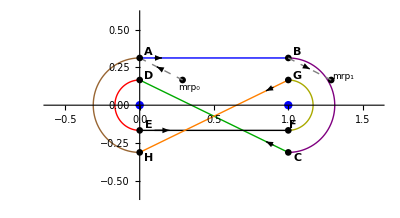

```mathematica
Show[{blueContourPlot,purpleContourPlot,greenContourPlot,redContourPlot,blackContourPlot,yellowContourPlot,orangeContourPlot,brownContourPlot,blueArrowG,greenArrowG,blackArrowG,orangeArrowG,zeroPointG,onePointG,mrp0G,mrpLine,pA,pAPoint,mrp0Point,mrp1Point,theArrowG,pB,pBPoint,pC,pCPoint,pD,pDPoint,pE,pEPoint,pF,pFPoint,pG,pH,pGPoint,pHPoint,mrp1G,mrpLine2,theArrowG2},PlotRange->{{-0.6,1.6},{-0.6,0.6}}]
```

## Notebook Section 5: Create cross-link table

```mathematica
(*
 automatic version 
*)
seriesResults=zeroBaseSeries/.z->pocR2 I;

totalBranches=functionDegree/theQ
branchSize=theQ
crossLinkTable=Table[
wStart=H[pocR2 I,wJ,wK];

difTable=N[Abs[wStart-#]&/@ seriesResults,10];
posArray=Position[difTable,Min@difTable];
mivPSeriesIndex=posArray[[1,1]];
(*
 get mIVP root associated with this series index ,
*)
mivTableIndex=(Position[zeroMIVTable,{mivPSeriesIndex,_}][[1]])[[1]];
monodromy=zeroMIVTable[[mivTableIndex,2,All,2]];
mivSeriesRecord=Cases[zeroMIVTable,{mivPSeriesIndex,_},Infinity][[1]];
(*Print["mivSeriesRecord: ",mivSeriesRecord]*)
mivRootIndex=mivSeriesRecord[[2]];
(*
 get branch name associated with this series 
*)
branchArrayPos=Position[zeroBranchTypeArray[[All,2]],x_/;x==mivPSeriesIndex][[1]];
branchName=zeroBranchTypeArray[[branchArrayPos[[1]],1]];

rootPosArray=Position[zeroMIVTable[[All,2,All,2]],x_/;x==mivRootIndex][[1]];

{wJ,wK,mivTableIndex,branchName,monodromy,mivPSeriesIndex,mivRootIndex},
{wK,0,totalBranches-1},
{wJ,0,branchSize-1}
];
crossTable=Partition[{#[[1]],#[[2]],#[[4]],#[[7]]}&/@Flatten[crossLinkTable,1],branchSize];
Labeled[Grid[Flatten@#&/@ crossTable,Dividers->{{{True,False,False,False}},{True,{False},True}}],Style["Cross link table"],Top]
```

7

3

0 | 0 | 7F_3^5 | 17 | 1 | 0 | 7F_3^5 | 12 | 2 | 0 | 7F_3^5 | 3
0 | 1 | 6F_3^5 | 14 | 1 | 1 | 6F_3^5 | 1 | 2 | 1 | 6F_3^5 | 15
0 | 2 | 4F_3^5 | 2 | 1 | 2 | 4F_3^5 | 13 | 2 | 2 | 4F_3^5 | 16
0 | 3 | 2F_3^5 | 11 | 1 | 3 | 2F_3^5 | 18 | 2 | 3 | 2F_3^5 | 4
0 | 4 | 1F_3^5 | 20 | 1 | 4 | 1F_3^5 | 6 | 2 | 4 | 1F_3^5 | 9
0 | 5 | 3F_3^5 | 8 | 1 | 5 | 3F_3^5 | 7 | 2 | 5 | 3F_3^5 | 21
0 | 6 | 5F_3^5 | 5 | 1 | 6 | 5F_3^5 | 19 | 2 | 6 | 5F_3^5 | 10Cross link table

## Section 12.6: Pre-processing

Select a (j,k) branch code and integrate from the monodromy reference point of s_1 to point A of the contour

### Section 6.1: Select branch code:

```mathematica
reim=Re;

wJ=2
wK=3
theAlpha
theBeta

initialSheetValue=H[1/3 Exp[Pi I/6],wJ,wK];
```

2

3

8/3

12/7

### Section 6.2: Integrate from mrp to point A of contour

```mathematica
(*
 now integrate from mrp to point A
*)
crossLinkTablePosition=Position[crossLinkTable,{wJ,wK,___}][[1]]
Print["crossLinkTableEntry: ",crossLinkTable[[Sequence@@crossLinkTablePosition]]];

branchFactor=Exp[2 wJ Pi I(theAlpha)] Exp[2 wK Pi I(theBeta)];
Print["branchFactor: ",branchFactor]

 w0=H[1/3 Exp[Pi I/6],wJ,wK];
mrpPath[t_]:=1/3 Exp[Pi I/6](1-t)+pocR2 I t;
wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[mrpPath[t],t])/.{w->w[t],z->mrpPath[t]});
mrpSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},WorkingPrecision->50];
pointAValue=mrpSol[1]
wList2=NSolveValues[theFunction==0/.z->pocR2 I,w,WorkingPrecision->50];
wList2//N
difTable2=Abs[#-pointAValue]&/@ wList2;
index2=Position[difTable2,Min@difTable2][[1,1]]
principalBranchAtA=wList2[[index2]]
(*
 index2 now has starting w0 for principal branch
*)
Precision@principalBranchAtA
```

{4,3}

crossLinkTableEntry: {2,3,2,2F_3^5,{4,11,18},4,4}

branchFactor: ⅇ^((20 ⅈ π)/21)

0.09369461968388424179670615736465512151492704655081-0.1155677197354221210190593118635921317798154905881 ⅈ

{-0.147289+0.0209886 ⅈ,-0.146932-0.0233581 ⅈ,-0.134559+0.0634703 ⅈ,-0.133519-0.0656293 ⅈ,-0.109873+0.100312 ⅈ,-0.108243-0.102069 ⅈ,-0.0754237+0.128241 ⅈ,-0.0733485-0.129439 ⅈ,-0.034273+0.144775 ⅈ,-0.0319368-0.145309 ⅈ,0.009923+0.148446 ⅈ,0.0123125-0.148267 ⅈ,0.0532373+0.138926 ⅈ,0.0554678-0.13805 ⅈ,0.0918212+0.117062 ⅈ,0.0936946-0.115568 ⅈ,0.122246+0.0847962 ⅈ,0.123596-0.0828164 ⅈ,0.141809+0.0449962 ⅈ,0.142516-0.0427065 ⅈ,0.148772+0.00119811 ⅈ}

16

0.09369461968388424179670614408702683962381045880325-0.11556771973542212101905959941864932187874632971887 ⅈ

50.

## Section 7: Integrate over Pochhammer contour and create branchLinkTable

```mathematica
(*
 Integrate over Pochhammer contour
*)
branchLinkTable={};

$stiffnessFlag=True;


wBlueStart=principalBranchAtA;

 blueContourF[t_]:=(pocR2 I)(1-t)+(1+pocR2 I) t;
blueStartT=0;
blueEndT=1;
Print["Integrating blue contour"];
{blueInt,bluePolishedEndW,blueTraceF}=integratePochhammer[blueContourF,0,1,wBlueStart,"stiffnessSwitching"->$stiffnessFlag];
(*
 get branch data at point A
*)
{branchName,mivPSeriesIndex,mivRootIndex,bluePlotIndex}=getBranchData[1,blueTraceF,blueContourF,zeroMIVTable,zeroBranchTypeArray,zeroBaseSeries,blueStartT,blueEndT];
AppendTo[branchLinkTable, {"A","s_1",branchName,mivPSeriesIndex,mivRootIndex,bluePlotIndex}];
(*
 plot solution trace
*)
blueTrace=ParametricPlot3D[{Re@z,Im@z,$reim@blueTraceF[t]}/.z->blueContourF[t],{t,blueStartT,blueEndT},PlotStyle->{Thickness[0.0055],Blue}];

(*
 do purple contour
*)
purpleContourF[t_]:=1+pocR2 Exp[I(Pi/2(1-t)+(-Pi/2) t)]; 
purpleStartT=0;
purpleEndT=1;

Print["Integrating purple contour"];
wPurpleStart=bluePolishedEndW;

{purpleInt,purplePolishedEndW,purpleTraceF}=integratePochhammer[purpleContourF,0,1,wPurpleStart,"stiffnessSwitching"->$stiffnessFlag];

purpleTrace=ParametricPlot3D[{Re@z,Im@z,reim@purpleTraceF[t]}/.z->purpleContourF[t],{t,purpleStartT,purpleEndT},PlotStyle->{Thickness[0.0055],Purple}];
 
(*
 get branch data at point B start of  purple contour
*){branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}=getBranchData[2,purpleTraceF,purpleContourF,oneMIVTable,oneBranchTypeArray,oneBaseSeries,purpleStartT,purpleEndT];
AppendTo[branchLinkTable, {"B","s_2",branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}];
(* 
 green contour
*)
greenStartT=0;
greenEndT=1;

greenContourF[t_]:=(1-pocR2 I)(1-t)+pocR1 I t;
wGreenStart=purplePolishedEndW;
Print["Integrating green contour"];
{greenInt,greenPolishedEndW,greenTraceF}=integratePochhammer[greenContourF,greenStartT,greenEndT,wGreenStart,"stiffnessSwitching"->$stiffnessFlag];
greenTrace=ParametricPlot3D[{Re@z,Im@z,reim@greenTraceF[t]}/.z->greenContourF[t],{t,greenStartT,greenEndT},PlotStyle->{Thickness[0.0055],Darker@Green}];
(*
 get branch data at start of green contour at point C
*)
{branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}=getBranchData[2,greenTraceF,greenContourF,oneMIVTable,oneBranchTypeArray,oneBaseSeries,greenStartT,greenEndT];
AppendTo[branchLinkTable, {"C","s_2",branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}];
(*
do red contour
*)
redContourF[t_]:=pocR1 Exp[I(Pi/2(1-t)+3 Pi/2 t)];
redStartT=0;
redEndT=1;

wRedStart=greenPolishedEndW;
Print["Integrating red contour"];
{redInt,redPolishedEndW,redTraceF}=integratePochhammer[redContourF,redStartT,redEndT,wRedStart,"stiffnessSwitching"->$stiffnessFlag];
(*
 get branch data at point D
*)
{branchName,mivPSeriesIndex,mivRootIndex,bluePlotIndex}=getBranchData[1,redTraceF,redContourF,zeroMIVTable,zeroBranchTypeArray,zeroBaseSeries,redStartT,redEndT];
redTrace=ParametricPlot3D[{Re@z,Im@z,reim@redTraceF[t]}/.z->redContourF[t],{t,redStartT,redEndT},PlotStyle->{Thickness[0.0055],Red}];
(*
 append branch data at point 
*)
AppendTo[branchLinkTable, {"D","s_1",branchName,mivPSeriesIndex,mivRootIndex,bluePlotIndex}];
(*
 do black contour
*)
blackContourF[t_]:=-pocR1 I(1-t)+(1-pocR1 I) t;
blackStartT=0;
blackEndT=1;
wBlackStart=redPolishedEndW;
Print["Integrating black contour"];
{blackInt,blackPolishedEndW,blackTraceF}=integratePochhammer[blackContourF,blackStartT,blackEndT,wBlackStart,"stiffnessSwitching"->$stiffnessFlag];
blackTrace=ParametricPlot3D[{Re@z,Im@z,reim@blackTraceF[t]}/.z->blackContourF[t],{t,blackStartT,blackEndT},PlotStyle->{Thickness[0.0055],Black}];
(*
 get branch data at start of black contour at point E
*)
{branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}=getBranchData[1,blackTraceF,blackContourF,zeroMIVTable,zeroBranchTypeArray,zeroBaseSeries,blackStartT,blackEndT];
AppendTo[branchLinkTable, {"E","s_1",branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}];


yellowContourF[t_]:=1+pocR1 Exp[I(-Pi/2(1-t)+Pi/2 t)];
yellowStartT=0;
yellowEndT=1;
wYellowStart=blackPolishedEndW;
Print["Integrating yellow contour"];
{yellowInt,yellowPolishedEndW,yellowTraceF}=integratePochhammer[yellowContourF,yellowStartT,yellowEndT,wYellowStart,"stiffnessSwitching"->$stiffnessFlag];

yellowTrace=ParametricPlot3D[{Re@z,Im@z,reim@yellowTraceF[t]}/.z->yellowContourF[t],{t,yellowStartT,yellowEndT},PlotStyle->{Thickness[0.0055],Yellow}];

(*
 get branch data at start of yellow contour at point F
*)
{branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}=getBranchData[2,yellowTraceF,yellowContourF,oneMIVTable,oneBranchTypeArray,oneBaseSeries,yellowStartT,yellowEndT];
AppendTo[branchLinkTable, {"F","s_2",branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}];
(*
 do orange contour
*)
 orangeContourF[t_]:=(1+pocR1 I)(1-t)+(-pocR2 I)t
orangeStartT=0;
orangeEndT=1;
wOrangeStart=yellowPolishedEndW;

Print["Integrating orange contour"];
{orangeInt,orangePolishedEndW,orangeTraceF}=integratePochhammer[orangeContourF,orangeStartT,orangeEndT,wOrangeStart,"stiffnessSwitching"->$stiffnessFlag];

orangeTrace=ParametricPlot3D[{Re@z,Im@z,reim@orangeTraceF[t]}/.z->orangeContourF[t],{t,orangeStartT,orangeEndT},PlotStyle->{Thickness[0.0055],Orange}];
(*
 get branch data at start of orange contour at point G
*)
{branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}=getBranchData[2,orangeTraceF,orangeContourF,oneMIVTable,oneBranchTypeArray,oneBaseSeries,orangeStartT,orangeEndT];
AppendTo[branchLinkTable, {"G","s_2",branchName,mivPSeriesIndex,mivRootIndex,purplePlotIndex}];

(*
 do brown contour
*)
brownStartT=0;
brownEndT=1;
 brownContourF[t_]:=pocR2 Exp[(3Pi/2) I(1-t)+(Pi/2 I(t))];

wBrownStart=orangePolishedEndW;
Print["Integrating brown contour"];
{brownInt,brownPolishedEndW,brownTraceF}=integratePochhammer[brownContourF,brownStartT,brownEndT,wBrownStart,"stiffnessSwitching"->$stiffnessFlag];
brownTrace=ParametricPlot3D[{Re@z,Im@z,reim@brownTraceF[t]}/.z->brownContourF[t],{t,brownStartT,brownEndT},PlotStyle->{Thickness[0.0055],Brown}];
(*
 get branch data at point H
*)
  {branchName,mivPSeriesIndex,mivRootIndex,brownPlotIndex}=getBranchData[1,brownTraceF,brownContourF,zeroMIVTable,zeroBranchTypeArray,zeroBaseSeries,orangeStartT,orangeEndT];
AppendTo[branchLinkTable, {"H","s_1",branchName,mivPSeriesIndex,mivRootIndex,brownPlotIndex}];



contourVal=Plus@@{blueInt,purpleInt,greenInt,redInt,blackInt,yellowInt,orangeInt,brownInt};
Print["contourVal: ",contourVal];
explicitContourVal=(branchFactor 4 Pi^2Exp[Pi I(theAlpha-theBeta)])/(Gamma[theAlpha+theBeta] Gamma[1-theAlpha] Gamma[1-theBeta]);
Print["explicit contour val: ",explicitContourVal//N];
Print["branch factor: ",branchFactor];

 

Print[Style["Mathematica's Beta result: ",Bold,Black],Beta[theAlpha,theBeta]//N]
contourResult=contourVal/(branchFactor(1-Exp[2 Pi I theAlpha])(1-Exp[-
2 Pi I theBeta]));
(*factorResults=contourResult/branchFactor ;*)
Print[Style["Beta Pochhammer contourResult: ",Bold,Black],contourResult//N]
(*Print["factorResults: ",factorResults//N]*)
(*Print["Offset contour result: ",contourResult//N]*)


Print["Contour accuracy: ",Abs[wBlueStart-brownPolishedEndW]];
(*Print["Beta Error: ",Abs[Beta[theAlpha,theBeta]-Exp[pocHFactors[[wRootIndex,2]]  2 Pi I /functionDegree]contourResult]]
*)
Print["crossLinkTableEntry: ",crossLinkTable[[Sequence@@crossLinkTablePosition]]];
(*Print[branchLinkTable[[All,1;;5]]//MatrixForm];
*)
branchLinkGrid=Labeled[Grid[Prepend[branchLinkTable[[All,1;;5]],{Column[{"Witness","point"},Alignment->Center],Column[{"Singular","point"},Alignment->Center],Column[{"Branch","name"},Alignment->Center],Column[{"Series","index"},Alignment->Center],Column[{"mIVP","root"},Alignment->Center]}],Dividers->{{{True}},{True,True,{False},True}}],Style["Branch link table"],Top]
```

Integrating blue contour

Integrating purple contour

Integrating green contour

Integrating red contour

Integrating black contour

Integrating yellow contour

Integrating orange contour

Integrating brown contour

contourVal: -0.3593282636952579666+0.1108380904526258188 ⅈ

explicit contour val: -0.359328+0.110838 ⅈ

branch factor: ⅇ^((20 ⅈ π)/21)

Mathematica's Beta result: 0.138843

Beta Pochhammer contourResult: 0.138843-1.68112×10^-11 ⅈ

Contour accuracy: 0.

crossLinkTableEntry: {2,3,2,2F_3^5,{4,11,18},4,4}

Witness
point | Singular
point | Branch
name | Series
index | mIVP
root
A | s_1 | 2F_3^5 | 4 | 4
B | s_2 | 2V_7^5 | 13 | 13
C | s_2 | 2V_7^5 | 13 | 13
D | s_1 | 4F_3^5 | 12 | 16
E | s_1 | 4F_3^5 | 10 | 2
F | s_2 | 1V_7^5 | 7 | 16
G | s_2 | 1V_7^5 | 7 | 16
H | s_1 | 2F_3^5 | 5 | 11Branch link table

## Section 8: Interactive viewer for testCase0039

```mathematica
branchLinkGrid
```

Witness
point | Singular
point | Branch
name | Series
index | mIVP
root
A | s_1 | 2F_3^5 | 4 | 4
B | s_2 | 2V_7^5 | 13 | 13
C | s_2 | 2V_7^5 | 13 | 13
D | s_1 | 4F_3^5 | 12 | 16
E | s_1 | 4F_3^5 | 10 | 2
F | s_2 | 1V_7^5 | 7 | 16
G | s_2 | 1V_7^5 | 7 | 16
H | s_1 | 2F_3^5 | 5 | 11Branch link table

```mathematica
zeroIndexes={1,4}
oneIndexes={2,6};
contourPlots={blueTrace,purpleTrace,greenTrace,redTrace,blackTrace,yellowTrace,orangeTrace,brownTrace};
branchNames={"A","B","C","D","E","F","G","H"};
pointA=pocR2 I;
 mrp=1/3 Exp[Pi I/6];
ip=H[1/3 Exp[Pi I/6],wJ,wK];
 initialPoint=Graphics3D@{PointSize[0.015],Red,Point@{Re@mrp,Im@mrp,$reim@ip}};
pointAG=Graphics3D@{PointSize[0.015],Green,Point@{Re@pointA,Im@pointA,$reim@pointAValue}};
mrpTrace=ParametricPlot3D[{Re@z,Im@z,$reim@mrpSol[t]}/.z->mrpPath[t],{t,0.1,0.9},PlotStyle->{Yellow},BoxRatios->{1, 1, 1},PlotRange->1];
zeroSeriesIndexes=branchLinkTable[[zeroIndexes,4]]
oneSeriesIndexes=branchLinkTable[[oneIndexes,4]]
Show[{initialPoint,mrpTrace,pointAG}]
```

{1,4}

{4,12}

{13,7}

-Graphics3D-

```mathematica
theContourPlots={blueTrace,purpleTrace,greenTrace,redTrace,blackTrace,yellowTrace,orangeTrace,brownTrace};
opac=0.3;
zeroColors={Red,Blue,Darker@Green,Darker@Yellow};
oneColors={Purple,Orange};
zeroColorIndex=0;

 zeroPlotTable=Table[
zeroColorIndex++;
 ParametricPlot3D[{Re@(z),Im@(z),$reim@zeroBaseSeries[[branchLinkTable[[bIndex,4]],1;;25]]}/.z->r Exp[I t],{t,-Pi,Pi},{r,1/20,1},PlotStyle->{Opacity[opac],zeroColors[[zeroColorIndex]]}],
{bIndex,zeroIndexes}
];
 oneColorIndex=0;
 onePlotTable=Table[
oneColorIndex++;
 ParametricPlot3D[{Re@(1+z),Im@(1+z),$reim@oneBaseSeries[[branchLinkTable[[bIndex,4]],1;;25]]}/.z->r Exp[I t],{t,-Pi,Pi},{r,1/20,1},PlotStyle->{Opacity[opac],oneColors[[oneColorIndex]]}],
{bIndex,oneIndexes}
];
```

```mathematica
z0=blueContourF[0];
w0=wBlueStart;

zB=purpleContourF[0];
wB=wPurpleStart;

zC=greenContourF[0];
wC=wGreenStart;

zD=redContourF[0];
wD=wRedStart;

zE=blackContourF[0];
wE=wBlackStart;

zF=yellowContourF[0];
wF=wYellowStart;

zG=orangeContourF[0];
wG=wOrangeStart;

zH=brownContourF[0];
wH=wBrownStart;


aText3D=Graphics3D@Text[Style["A",12,Black,Bold],{Re@(z0-0.1),Im@(z0+0.05),Re@w0}];
bText3D=Graphics3D@Text[Style["B",12,Black,Bold],{Re@(zB),Im@zB+0.1,Re@wB}];
cText3D=Graphics3D@Text[Style["C",12,Black,Bold],{Re@(zC+0.1),Im@(zC-0.05),Re@wC}];
dText3D=Graphics3D@Text[Style["D",12,Black,Bold],{Re@(zD+0.1),Im@(zD+0.05),Re@wD}];
eText3D=Graphics3D@Text[Style["E",12,Black,Bold],{Re@(zE+0.1),Im@(zE+0.05),Re@wE-0.05}];
fText3D=Graphics3D@Text[Style["F",12,Black,Bold],{Re@(zF+0.1),Im@(zF+0.05),Re@wF}];
gText3D=Graphics3D@Text[Style["G",12,Black,Bold],{Re@(zG+0.1),Im@(zG+0.05),Re@wG}];
hText3D=Graphics3D@Text[Style["H",12,Black,Bold],{Re@(zH+0.1),Im@(zH+0.05),Re@wH}];

contourLabelArray={aText3D,bText3D,cText3D,dText3D,eText3D,fText3D,gText3D,hText3D};
```

```mathematica
Row[{ Manipulate[
Show[Pick[zeroPlotTable,{u1,u2}],Pick[onePlotTable,{v1,v2}],Pick[theContourPlots,{blue,purple,green,red,black,yellow,orange,brown}],(*contourLabelArray,*)(*,branchID,branchID2 ,branchID3*)AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},*)AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All,ViewPoint->{-0.3652403481483002,-2.414641458398215,2.342243820670481}],
   Grid[{{Style["Series indexes",12,Black,Bold],SpanFromLeft,SpanFromLeft},{"",Style["s_1",12,Bold,Black],"","",Style["s_2",12,Bold,Black]},
{Checkbox[Dynamic[u1,{u1=#}&]],Style[zeroSeriesIndexes[[1]],12,Red],Spacer[5],Checkbox[Dynamic[v1,{v1=#}&]],Style[oneSeriesIndexes[[1]],12,Purple]},
{Checkbox[Dynamic[u2,{u2=#}&]],Style[zeroSeriesIndexes[[2]],12,Blue],Spacer[5],Checkbox[Dynamic[v2,{v2=#}&]],Style[oneSeriesIndexes[[2]],12,Orange]}
}],
{{u1,True},None},{{v1,True},None},
{{u2,False},None},{{v2,False},None},
Spacer[5],
Grid[{{"",Style["Contours",12,Black,Bold]},
{Checkbox[Dynamic[blue,{blue=#}&]],Style["Blue",12,Blue]},
{Checkbox[Dynamic[purple,{purple=#}&]],Style["Purple",12,Purple]},
{Checkbox[Dynamic[green,{green=#}&]],Style["Green",12,Darker@Green]},
{Checkbox[Dynamic[red,{red=#}&]],Style["Red",12,Red]},
{Checkbox[Dynamic[black,{black=#}&]],Style["Black",12,Black]},
{Checkbox[Dynamic[yellow,{yellow=#}&]],Style["Yellow",12,Darker@Yellow]},
{Checkbox[Dynamic[orange,{orange=#}&]],Style["Orange",12,Orange]},
{Checkbox[Dynamic[brown,{brown=#}&]],Style["Brown",12,Darker@Brown]}
}],
{{blue,True},None},{{purple,True},None},
{{green,False},None},{{red,False},None},
{{black,False},None},{{yellow,False},None},
{{orange,False},None},{{brown,False},None},

TrackedSymbols:>{u1,v1,u2,v2,blue,purple,green,red,black,yellow,orange,brown},
ControlPlacement->Right],Spacer[5],branchLinkGrid,Spacer[5]},Background->White,Frame->True]
```

Witness
point | Singular
point | Branch
name | Series
index | mIVP
root
A | s_1 | 2F_3^5 | 4 | 4
B | s_2 | 2V_7^5 | 13 | 13
C | s_2 | 2V_7^5 | 13 | 13
D | s_1 | 4F_3^5 | 12 | 16
E | s_1 | 4F_3^5 | 10 | 2
F | s_2 | 1V_7^5 | 7 | 16
G | s_2 | 1V_7^5 | 7 | 16
H | s_1 | 2F_3^5 | 5 | 11Branch link table

```mathematica
Options[-Graphics3D-,ViewPoint]
```

{ViewPoint→{-0.36524,-2.41464,2.34224}}

## Section 9: Interactive viewer for testCase0043

```mathematica
branchLinkGrid
```

Witness
point | Singular
point | Branch
name | Series
index | mIVP
root
A | s_1 | 2F_3^5 | 4 | 4
B | s_2 | 2V_7^5 | 13 | 13
C | s_2 | 2V_7^5 | 13 | 13
D | s_1 | 4F_3^5 | 12 | 16
E | s_1 | 4F_3^5 | 10 | 2
F | s_2 | 1V_7^5 | 7 | 16
G | s_2 | 1V_7^5 | 7 | 16
H | s_1 | 2F_3^5 | 5 | 11Branch link table

```mathematica
zeroIndexes={1,4,5,8}
oneIndexes={2,6};
contourPlots={blueTrace,purpleTrace,greenTrace,redTrace,blackTrace,yellowTrace,orangeTrace,brownTrace};
branchNames={"A","B","C","D","E","F","G","H"};
pointA=pocR2 I;
 mrp=1/3 Exp[Pi I/6];
ip=H[1/3 Exp[Pi I/6],wJ,wK];
 initialPoint=Graphics3D@{PointSize[0.015],Red,Point@{Re@mrp,Im@mrp,$reim@ip}};
pointAG=Graphics3D@{PointSize[0.015],Green,Point@{Re@pointA,Im@pointA,$reim@pointAValue}};
mrpTrace=ParametricPlot3D[{Re@z,Im@z,$reim@mrpSol[t]}/.z->mrpPath[t],{t,0.1,0.9},PlotStyle->{Yellow},BoxRatios->{1, 1, 1},PlotRange->1];
zeroSeriesIndexes=branchLinkTable[[zeroIndexes,4]]
oneSeriesIndexes=branchLinkTable[[oneIndexes,4]]
Show[{initialPoint,mrpTrace,pointAG}]
```

{1,4,5,8}

{4,12,10,5}

{13,7}

-Graphics3D-

```mathematica
theContourPlots={blueTrace,purpleTrace,greenTrace,redTrace,blackTrace,yellowTrace,orangeTrace,brownTrace};
opac=0.3;
zeroColors={Red,Blue,Darker@Green,Darker@Yellow};
oneColors={Purple,Orange};
zeroColorIndex=0;

 zeroPlotTable=Table[
zeroColorIndex++;
 ParametricPlot3D[{Re@(z),Im@(z),$reim@zeroBaseSeries[[branchLinkTable[[bIndex,4]],1;;5]]}/.z->r Exp[I t],{t,-Pi,Pi},{r,1/20,1},PlotStyle->{Opacity[opac],zeroColors[[zeroColorIndex]]}],
{bIndex,zeroIndexes}
];
 oneColorIndex=0;
 onePlotTable=Table[
oneColorIndex++;
 ParametricPlot3D[{Re@(1+z),Im@(1+z),$reim@oneBaseSeries[[branchLinkTable[[bIndex,4]],1;;5]]}/.z->r Exp[I t],{t,-Pi,Pi},{r,1/20,1},PlotStyle->{Opacity[opac],oneColors[[oneColorIndex]]}],
{bIndex,oneIndexes}
];
```

```mathematica
z0=blueContourF[0];
w0=wBlueStart;

zB=purpleContourF[0];
wB=wPurpleStart;

zC=greenContourF[0];
wC=wGreenStart;

zD=redContourF[0];
wD=wRedStart;

zE=blackContourF[0];
wE=wBlackStart;

zF=yellowContourF[0];
wF=wYellowStart;

zG=orangeContourF[0];
wG=wOrangeStart;

zH=brownContourF[0];
wH=wBrownStart;


aText3D=Graphics3D@Text[Style["A",12,Black,Bold],{Re@(z0-0.1),Im@(z0+0.05),Re@w0}];
bText3D=Graphics3D@Text[Style["B",12,Black,Bold],{Re@(zB),Im@zB+0.1,Re@wB}];
cText3D=Graphics3D@Text[Style["C",12,Black,Bold],{Re@(zC+0.1),Im@(zC-0.05),Re@wC}];
dText3D=Graphics3D@Text[Style["D",12,Black,Bold],{Re@(zD+0.1),Im@(zD+0.05),Re@wD}];
eText3D=Graphics3D@Text[Style["E",12,Black,Bold],{Re@(zE+0.1),Im@(zE+0.05),Re@wE-0.05}];
fText3D=Graphics3D@Text[Style["F",12,Black,Bold],{Re@(zF+0.1),Im@(zF+0.05),Re@wF}];
gText3D=Graphics3D@Text[Style["G",12,Black,Bold],{Re@(zG+0.1),Im@(zG+0.05),Re@wG}];
hText3D=Graphics3D@Text[Style["H",12,Black,Bold],{Re@(zH+0.1),Im@(zH+0.05),Re@wH}];

contourLabelArray={aText3D,bText3D,cText3D,dText3D,eText3D,fText3D,gText3D,hText3D};
```

```mathematica
Show[Pick[zeroPlotTable,{True,False,False,False}],Pick[onePlotTable,{False,False}]]
```

-Graphics3D-

```mathematica
Row[{ Manipulate[
Show[Pick[zeroPlotTable,{u1,u2,u3,u4}],Pick[onePlotTable,{v1,v2}],Pick[theContourPlots,{blue,purple,green,red,black,yellow,orange,brown}],(*contourLabelArray,*)(*,branchID,branchID2 ,branchID3*)AxesEdge->{{-1,-1},{1,-1},{-1,-1}},Axes->True,(*FaceGrids->{{{0,0,-1},{xGrids,yGrids}}},*)AxesLabel->{Style["Re[z]",12,Bold,Black],Style["Im[z]",12,Bold,Black],Style["Re(w)",12,Bold,Black]},FaceGridsStyle->Directive[Black,Dotted],BoxRatios->{1, 1,1},PlotRange->All,ViewPoint->{-0.3652403481483002,-2.414641458398215,2.342243820670481}],
   Grid[{{Style["Series indexes",12,Black,Bold],SpanFromLeft,SpanFromLeft},{"",Style["s_1",12,Bold,Black],"","",Style["s_2",12,Bold,Black]},
{Checkbox[Dynamic[u1,{u1=#}&]],Style[zeroSeriesIndexes[[1]],12,Red],Spacer[5],Checkbox[Dynamic[v1,{v1=#}&]],Style[oneSeriesIndexes[[1]],12,Purple]},
{Checkbox[Dynamic[u2,{u2=#}&]],Style[zeroSeriesIndexes[[2]],12,Blue],Spacer[5],Checkbox[Dynamic[v2,{v2=#}&]],Style[oneSeriesIndexes[[2]],12,Orange]},

{Checkbox[Dynamic[u3,{u3=#}&]],Style[zeroSeriesIndexes[[3]],12,Darker@Green]},
{Checkbox[Dynamic[u4,{u4=#}&]],Style[zeroSeriesIndexes[[4]],12,Darker@Yellow]}

}],
{{u1,True},None},{{v1,True},None},
{{u2,False},None},{{v2,False},None},
{{u3,False},None},
{{u4,False},None},
Spacer[5],
Grid[{{"",Style["Contours",12,Black,Bold]},
{Checkbox[Dynamic[blue,{blue=#}&]],Style["Blue",12,Blue]},
{Checkbox[Dynamic[purple,{purple=#}&]],Style["Purple",12,Purple]},
{Checkbox[Dynamic[green,{green=#}&]],Style["Green",12,Darker@Green]},
{Checkbox[Dynamic[red,{red=#}&]],Style["Red",12,Red]},
{Checkbox[Dynamic[black,{black=#}&]],Style["Black",12,Black]},
{Checkbox[Dynamic[yellow,{yellow=#}&]],Style["Yellow",12,Darker@Yellow]},
{Checkbox[Dynamic[orange,{orange=#}&]],Style["Orange",12,Orange]},
{Checkbox[Dynamic[brown,{brown=#}&]],Style["Brown",12,Darker@Brown]}
}],
{{blue,True},None},{{purple,True},None},
{{green,False},None},{{red,False},None},
{{black,False},None},{{yellow,False},None},
{{orange,False},None},{{brown,False},None},

TrackedSymbols:>{u1,v1,u2,v2,u3,u4,blue,purple,green,red,black,yellow,orange,brown},
ControlPlacement->Right],Spacer[5],branchLinkGrid,Spacer[5]},Background->White,Frame->True]
```

Witness
point | Singular
point | Branch
name | Series
index | mIVP
root
A | s_1 | 2F_3^5 | 4 | 4
B | s_2 | 2V_7^5 | 13 | 13
C | s_2 | 2V_7^5 | 13 | 13
D | s_1 | 4F_3^5 | 12 | 16
E | s_1 | 4F_3^5 | 10 | 2
F | s_2 | 1V_7^5 | 7 | 16
G | s_2 | 1V_7^5 | 7 | 16
H | s_1 | 2F_3^5 | 5 | 11Branch link table

```mathematica
Options[-Graphics3D-,ViewPoint]
```

{ViewPoint→{-0.36524,-2.41464,2.34224}}

## Initialization

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]];
 $HistoryLength=0;
$thetaV=Pi/6;
$reim=Re;
colorNumbers=Join[{14,60,45,57,24,35,43,45,32,16,32,15,17,2,7,3,14,18,21,60,45,57,21,35,43,45,32,16,32,15,17,19,12,37,49,15,7,9,13},Range[42]];

theColorList=Table[ColorData[colorNumbers[[i]],"ColorList"],{i,1,Length[colorNumbers]}];
(*theRGBColors=theColorList/.GrayLevel[azz__]->ColorConvert[GrayLevel[azz],"RGB"];
mycolors=theRGBColors/.RGBColor[az_,bz_,cz_]-> {az,bz,cz};
*)
branchColors=Join[{Red,Blue,Darker@Green,Darker@Yellow,Purple,Orange,Magenta,Pink},Flatten@theColorList[[5;;10]]];

defaultColors={Black,Blue,Brown,Cyan,Gray,Green,Magenta,Orange,Pink,Purple,Red,Yellow};
```

### Setup file names

```mathematica
realPlotDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\realSingularPlot"<>StringTake[testCase,-4;;]<>".m"}];
  imagPlotDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase<>"\\imagSingularPlot"<>StringTake[testCase,-4;;]<>".m"}];
   singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singularData.m"}] ;
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];

annularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\annularMonodromies.m"}];
annularMonodromyTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\annularMonodromyTableFileName.m"}]; 
annularMonodromyTableGraphicsFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\annularMonodromyTableGraphics.jpg"}]; 

 singularMonodromyFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"\\singularMonodromies.m"}];
summatorySeriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`summatorySeries.m"][testCase,ToString@k]}];



annularIntegrationDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularIntegrationData.m"}];

annularTableWithMonodromiesFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithMonodromies.m"}];
```

### integratePochhammer

```mathematica
Options[integratePochhammer]={"stiffnessSwitching"->False};
 integratePochhammer[contourF_,startT_,endT_,startW_,OptionsPattern[]]:=Module[{startZ,contourTraceF,endW,endZ,intVal,polishedEndW},
startZ=contourF[startT];
contourTraceF=ndSolveOverBranch[contourF,startW,startT,endT,"stiffnessSwitching"->OptionValue["stiffnessSwitching"]];
(*Print[" precision of contourTraceF: ",Precision@contourTraceF[t]];*)
startZ=contourF[startT];
endZ=contourF[endT];
endW=contourTraceF[endT];
intVal=NIntegrate[contourTraceF[t] D[contourF[t],t],{t,startT,endT},WorkingPrecision->20];

polishedEndW=polishValue[endZ,endW,75];
{intVal,polishedEndW,contourTraceF}

]
```

### ndSolveOverBranch

```mathematica
Options[ndSolveOverBranch]={"stiffnessSwitching"->False};
  ndSolveOverBranch[contour_,wStart_,tStart_,tEnd_,OptionsPattern[]]:=Module[{wDeriv},
wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) (D[contour[t],t]))/.{w->w[t],z->contour[t]});
If[OptionValue["stiffnessSwitching"],
NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->1000000,MaxStepSize->1/1000,PrecisionGoal->55,WorkingPrecision->50,Method->"StiffnessSwitching"]
,
NDSolveValue[{wDeriv,w[tStart]==wStart},w,{t,tStart,tEnd},MaxSteps->1000000,MaxStepSize->1/1000,PrecisionGoal->55,WorkingPrecision->50]
]
]
```

### polishValues

```mathematica
polishValue[zVal_,wVal_,wp_]:=Module[{wTemp,difArray,wPos,eqnPrecision},
eqnPrecision=Floor@Precision@(theFunction==0/.z->zVal);
 wTemp=w/.NSolve[theFunction==0/.z->zVal,w,WorkingPrecision->eqnPrecision];
difArray=Abs[wVal-#]&/@ wTemp;
wPos=Position[difArray,Min@difArray][[1,1]];
If[difArray[[wPos]]>10^-6,
Print[Style["polishValue: min dif array>10^-9",Red]];
Print["difArray: ",difArray//N];
Print["  minDif: ",N[difArray[[wPos]],10]];
];
wTemp[[wPos]]
];
```

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];

aForm2[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[c]@*thecRules[c]]@toPowerBoxes[z]@thecRules[z][f];
```

### getPochhammerMonodromy

```mathematica
(*
 get differential monodromy around a singular point
*)
Options[getPochhammerMonodromy]={"nSolveWP"->50,"integrateWP"->50,"polishWP"->20,"diagFlag"->False};
getPochhammerMonodromy[singularPoint_,perimeter_,OptionsPattern[]]:=Module[{z0,singularRoots,wArray,branchVals,polishedVals,pArray,theCycles,theLinks,oneCycles,finalCycles},
Print["nSolveWP: ",OptionValue["nSolveWP"]];
z0=singularPoint+perimeter Exp[Pi I/2];
Print["z0: ",z0//N];
singularRoots=Sort[w/.NSolve[theFunction==0/.z->z0,w,WorkingPrecision->OptionValue["nSolveWP"]]];
wArray=MapThread[{#1,#2}&,{Range[Length@singularRoots],singularRoots}];


 branchVals=integrateOverPochhammerSheet[z0,singularPoint,Pi/2,wArray,perimeter,False,OptionValue["integrateWP"]];


polishedVals=polishBranchTerms[z0,branchVals,OptionValue["polishWP"]];
If[OptionValue["diagFlag"],
Print["polishedVals: ",polishedVals//N//MatrixForm];
];
(* *)
pArray=Flatten[Position[polishedVals[[All,2]],x_/;Abs[x-#]<10^-20]&/@ polishedVals[[All,3]]];

theCycles=PermutationCycles[pArray];
theLinks=theCycles[[1]];
oneCycles={#}&/@Complement[Range[functionDegree],Flatten[theLinks]];
finalCycles=Join[theLinks,oneCycles];

If[Sort[Flatten@finalCycles]!=Range[Length@Flatten@finalCycles],
Print[Style["Monodromy is not consistent!",Purple,14]];
,
Print[Style["Monodromy is consistent",Darker@Green,12]];
];
{finalCycles,polishedVals}
]
```

### integrateOverSheet

```mathematica
integrateOverPochhammerSheet[startPoint_,singPoint_,startTheta_,w0Table_,radius_,stiffnessFlag_,wp_]:=Module[{intTable,integrationPath,wDeriv,theSol,w0},
PrintTemporary["Integrating index ",Dynamic@np];
 intTable=Table[
np=n;
w0=w0Table[[n,2]];
integrationPath[t_]:=singPoint+radius Exp[I t];
wDeriv=w'[t]==((-(D[theFunction,z]/D[theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[stiffnessFlag,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[startTheta]==w0},w,{t,startTheta,startTheta+2 Pi},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->wp];
];
(* save {seriesIndex,theSol[1]} *)
{w0Table[[n,1]],w0Table[[n,2]],theSol[startTheta+2 Pi]},
{n,1,Length@w0Table}
];
intTable
];
```

### polishBranchTerms

```mathematica
polishBranchTerms[zVal_,terms_,maxErrorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

termsPrec=Floor@Precision@terms[[All,2]];
wVals=w/.NSolve[theFunction==0/.z->zVal,w,WorkingPrecision->termsPrec];
polishedValues=Table[
difTable=Abs[terms[[i,3]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-maxErrorTolerance),
Print[Style["polishTerms error below $maxErrorTolerance: ",Red,Bold,14]];
Print["     difTable: ",difTable//N];
];
{terms[[i,1]],terms[[i,2]],wVals[[pos]]},
{i,1,Length@terms}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### getBranchData

```mathematica
getBranchData[singularIndex_,contourTrace_,contourF_,mivTable_,branchNameArray_,series_,tStart_,tEnd_]:=Module[{zStart,wEnd,seriesResults,difTable,mivPSeriesIndex,mivSeriesRecord,mivRootIndex,branchArrayPos,branchName,rootPosArray,plotIndex,wStart,posArray},
zStart=contourF[tStart];
wStart=  polishValue[zStart,contourTrace[tStart],55];
(*
 determine which Puiseux series wStart lands on at mIVP point
*)
seriesResults=series/.z->(zStart-theSingularList[[singularIndex]]);
difTable=N[Abs[wStart-#]&/@ seriesResults,10];
posArray=Position[difTable,Min@difTable];
mivPSeriesIndex=posArray[[1,1]];
(*
 get mIVP root associated with this series index ,
*)
mivSeriesRecord=Cases[mivTable,{mivPSeriesIndex,_},Infinity][[1]];
mivRootIndex=mivSeriesRecord[[2]];
(*
 get branch name associated with this series 
*)
branchArrayPos=Position[branchNameArray[[All,2]],x_/;x==mivPSeriesIndex][[1]];
branchName=branchNameArray[[branchArrayPos[[1]],1]];
rootPosArray=Position[mivTable[[All,2,All,2]],x_/;x==mivRootIndex][[1]];
plotIndex=rootPosArray[[1]];

{branchName,mivPSeriesIndex,mivRootIndex,plotIndex}
]
```

```mathematica
Options[getBranchData]={"diag"->False};

getBranchData2[currentSingularIndex_,mivTable_,branchNameArray_,currentSeries_,currentZStart_,currentWStart_,tStart_,tEnd_,OptionsPattern[]]:=Module[{contour,branchSol,zEnd,wEnd,seriesResults,difTable,mivPSeriesIndex,branchArrayPos,branchName, mivSeriesRecord,mivRootIndex,plotIndex,branchNamePos,rootPosArray},
 contour[t_]:=currentZStart(1-t)+(theSingularList[[currentSingularIndex]]+minRadiusArray[[currentSingularIndex]] Exp[Pi I/6]) t;
(*
 integrate to mIVP point at this singular point and polish value
*)
Print["currentWStart: ",currentWStart];
 branchSol=ndSolveOverBranch[contour,currentWStart,tStart,tEnd];
zEnd=contour[tEnd];
wEnd=  polishValue[zEnd,branchSol[tEnd],55];
(*
 determine which Puiseux series blue contour lands on at mIVP point
*)
seriesResults=currentSeries/.z->(zEnd-theSingularList[[currentSingularIndex]]);
difTable=N[Abs[wEnd-#]&/@ seriesResults,10];

mivPSeriesIndex=Position[difTable,Min@difTable][[1,1]];
If[OptionValue["diag"],
Print["mivPSeriesIndex: ",mivPSeriesIndex];
Print["Min dif: ",N[difTable[[mivPSeriesIndex]]]];
];
(*
 get mIVP root associated with this series index ,
*)
mivSeriesRecord=Cases[mivTable,{mivPSeriesIndex,_},Infinity][[1]];
mivRootIndex=mivSeriesRecord[[2]];
If[OptionValue["diag"],
Print["mivRootIndex associated with this series: ",mivRootIndex];
Print["mivTable: ",mivTable]
];
(*
 get branch name associated with this series
*)
branchArrayPos=Position[branchNameArray[[All,2]],x_/;x==mivPSeriesIndex][[1]];
branchName=branchNameArray[[branchArrayPos[[1]],1]];
rootPosArray=Position[mivTable[[All,2,All,2]],x_/;x==mivRootIndex][[1]];
plotIndex=rootPosArray[[1]];

{branchName,mivPSeriesIndex,mivRootIndex,plotIndex}


];
```